```mathematica
<<MaTeX`;
ConfigureMaTeX["pdfLaTeX" -> "/usr/bin/pdflatex"];

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{color,txfonts}","\\usepackage[usenames,dvipsnames]{xcolor}","\\usepackage[makeroom]{cancel}","\\usepackage{ulem}","\\usepackage{booktabs}","\\usepackage{multirow}","\\usepackage{rotating}","\\setcounter{MaxMatrixCols}{20}"}];
```

# 1 DOF systems

## Stable symmetrical post-critical system

## Sistema perfetto

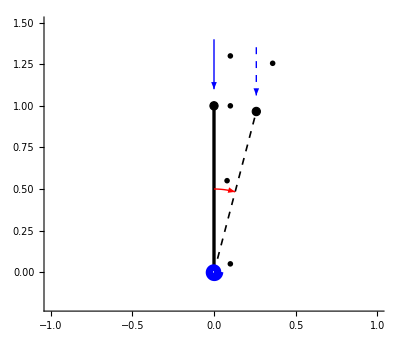

```mathematica
l=1;

carh=Graphics[Triangle[{{-1/2,-1},{0,0},{1/2,-1}}]];
cer=Graphics[{FaceForm[White],EdgeForm[Directive[Thick]],Disk[{0,0},1]}];
myCircle[o_,r_,{a_,b_},res_]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];
rspring[centre_,rounds_,radius_]:=Module[{},
x[t_]:=radius/rounds/(2*Pi)*t*Cos[t];
y[t_]:=radius/rounds/(2*Pi)*t*Sin[t];
ParametricPlot[{centre[[1]]+x[t],centre[[2]]+y[t]},{t,0,rounds*2*Pi},PlotStyle->Blue]
];

Show[{
Graphics[{Thickness[0.006],Line[{{0,0},{l*Sin[θ],l*Cos[θ]}/.θ->0}]}],
Graphics[{Thickness[0.003],Dashed,Line[{{0,0},{l*Sin[θ],l*Cos[θ]}/.θ->15 Degree}]}],
Graphics[{Inset[cer,{0,0},{0,0},0.05]}],
rspring[{0,0},4,0.05],
Graphics[Text[MaTeX["\\textcolor{blue}{K}",Magnification->2],{0.1,0.05}*l]],
Graphics[{Thick,Blue,Arrow[l*{{0,1.4},{0,1.1}}]}],
Graphics[Text[MaTeX["\\textcolor{blue}{P}",Magnification->2],{0.1,1.3}*l]],
Graphics[{Thick,Dashed,Blue,Arrow[{{l*Sin[θ],1.4*l*Cos[θ]}/.θ->15 Degree,{l*Sin[θ],1.1*l*Cos[θ]}/.θ->15 Degree}]}],
Graphics[Text[MaTeX["\\textcolor{blue}{P}",Magnification->2],{l*Sin[θ]+0.1,1.3*l*Cos[θ]}/.θ->15 Degree]],
Graphics[{FaceForm[Black],EdgeForm[Directive[Thick]],Disk[{0,l},0.025]}],
Graphics[{FaceForm[Black],EdgeForm[Directive[Thick]],Disk[{l*Sin[θ],l*Cos[θ]}/.θ->15 Degree,0.025]}],
Graphics[Text[MaTeX["m",Magnification->2],{0.1,1.}*l]],
Graphics[{Red,Thick,Arrowheads[0.03],myCircle[{0,0},0.5*l,{90 Degree,75 Degree},10]}],
Graphics[Text[MaTeX["\\textcolor{red}{\\theta}",Magnification->2],{0.08,0.55}*l]]
},
PlotRange->{{-l,l},{-0.2*l,1.5*l}},
Axes->True,
ImageSize->{Automatic,500}]
```

### Energetic method

```mathematica
ClearAll[θ, Ε, W, V, dV, λ, τ, H, λ0];
Ε[θ_]= 1/2 θ^2;
W[λ_,θ_]= λ*(1-Cos[θ]);
V[λ_,θ_]= Ε[θ] - W[λ,θ]

dV[λ_,θ_]= D[V[λ,θ], θ]
λ0 [θ_]= λ/.Solve[dV[λ, θ] == 0, λ][[1]]

Show[Plot3D[V[λ, θ], {λ, 0, 2}, {θ, -Pi, Pi}, AxesLabel->{"(P l)/K","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
ParametricPlot3D[{λ0[θ],θ,V[λ0[θ],θ]},{θ,-π,π}],ParametricPlot3D[{λ,0,V[λ,0]},{λ,0,2}], ImageSize->Large]
```

θ^2/2-λ (1-Cos[θ])

θ-λ Sin[θ]

θ Csc[θ]

-Graphics3D-

```mathematica
ClearAll[d2V]
d2V[λ_, θ_]= D[dV[λ, θ], θ]
d2V[λ, θ]/.λ->λ0[θ]
```

1-λ Cos[θ]

1-θ Cot[θ]

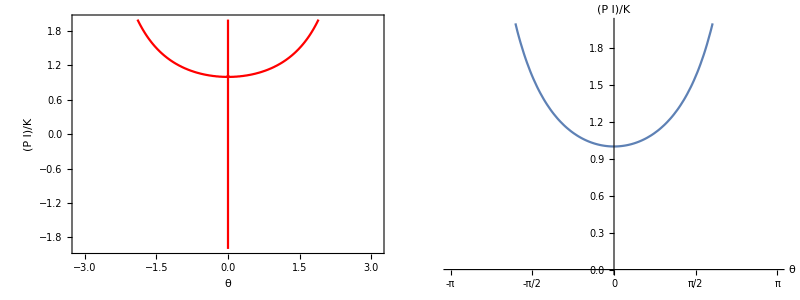

```mathematica
Grid[
{{
Show[
ContourPlot[dV[λ,θ]==0, {θ, -Pi, Pi}, {λ, -2, 2}, ContourStyle->Red, PlotPoints->50, FrameLabel->{"θ", "(P l)/K"},LabelStyle->18],
RegionPlot[d2V[λ, θ]>0, {θ, -Pi,Pi}, {λ, -2, 2}, Axes->True, Ticks->{Table[k*Pi, {k, -1, 1, 1/4}], Automatic}, GridLines->None], ImageSize->Medium
],
Plot[{λ0[θ]}, {θ, -Pi/1, Pi/1}, PlotRange->{Automatic, {0,2}},   Ticks->{{-Pi,-3/4 Pi,-Pi/2, -Pi/4, 0, Pi/4, Pi/2, 3/4 Pi, Pi},Automatic}, AxesLabel->{"θ", "(P l)/K"},LabelStyle->18,  ImageSize->Medium]
}},
Spacings->8
]
```

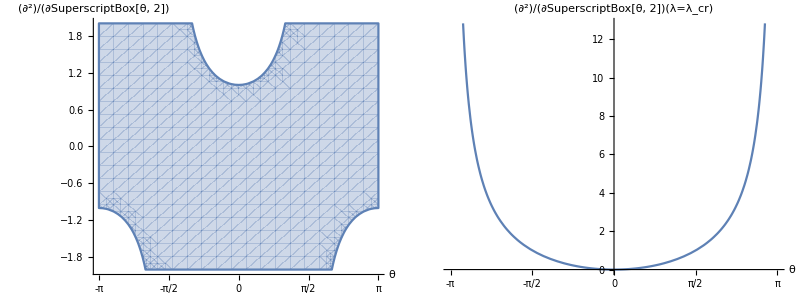

```mathematica
Grid[{{
RegionPlot[d2V[λ, θ]>0, {θ, -Pi,Pi}, {λ, -2, 2}, Axes->True, AxesLabel->{"θ", "∂^2/(∂SuperscriptBox[θ, 2])"},LabelStyle->18, Ticks->{Table[k*Pi, {k, -1, 1, 1/4}], Automatic}, GridLines->None, Frame->False, ImageSize->Medium], 
Plot[d2V[λ0[θ], θ],{θ, -Pi,Pi}, Ticks->{Table[k*Pi, {k, -1, 1, 1/4}], Automatic}, AxesLabel->{"θ", "∂^2/(∂SuperscriptBox[θ, 2])(λ=λ_cr)"},LabelStyle->18, ImageSize->Medium
]}}, Spacings->5]
```

### Dynamic method

```mathematica
ClearAll[θ, Ε, W, V, dV, λ, τ, H, λ0];
τ[θp_]= 1/2 θp^2;
Ε[θ_]= 1/2 θ^2;
W[λ_,θ_]= λ*(1-Cos[θ]);
V[λ_,θ_]= Ε[θ] - W[λ,θ];
W[λ_,θ_]= λ*(1-Cos[θ]);
H[λ_,θ_, θp_]= τ[θp] + V[λ,θ]
```

θ^2/2+θp^2/2-λ (1-Cos[θ])

```mathematica
Grid[{{
Manipulate[Plot3D[H[λ,θ, θp], {θ, -Pi, Pi}, {θp, -5, 5}, AxesLabel->{"θ", "dθ/dt", "H"}],{{λ,0,"(P l)/K"}, 0, 2,.1} ],
Manipulate[ContourPlot[H[λ,θ, θp], {θ, -Pi, Pi}, {θp, -5, 5}, FrameLabel->{"θ", "dθ/dt"}], {{λ,0,"(P l)/K"}, 0, 2,.1} ]
}},Spacings->5]
```

|

## Imperfezione di rotazione iniziale θ_0

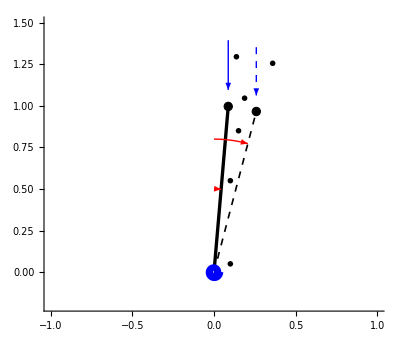

```mathematica
l=1;

carh=Graphics[Triangle[{{-1/2,-1},{0,0},{1/2,-1}}]];
cer=Graphics[{FaceForm[White],EdgeForm[Directive[Thick]],Disk[{0,0},1]}];
myCircle[o_,r_,{a_,b_},res_]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];
rspring[centre_,rounds_,radius_]:=Module[{},
x[t_]:=radius/rounds/(2*Pi)*t*Cos[t];
y[t_]:=radius/rounds/(2*Pi)*t*Sin[t];
ParametricPlot[{centre[[1]]+x[t],centre[[2]]+y[t]},{t,0,rounds*2*Pi},PlotStyle->Blue]
];

Show[{
Graphics[{Thickness[0.006],Line[{{0,0},{l*Sin[θ],l*Cos[θ]}/.θ->5 Degree}]}],
Graphics[{Thickness[0.003],Dashed,Line[{{0,0},{l*Sin[θ],l*Cos[θ]}/.θ->15 Degree}]}],
Graphics[{Inset[cer,{0,0},{0,0},0.05]}],
rspring[{0,0},4,0.05],
Graphics[Text[MaTeX["\\textcolor{blue}{K}",Magnification->2],{0.1,0.05}*l]],
Graphics[{Thick,Blue,Arrow[l*{{l*Sin[θ],1.4*l*Cos[θ]},{l*Sin[θ],1.1*l*Cos[θ]}}/.θ-> 5 Degree]}],
Graphics[Text[MaTeX["\\textcolor{blue}{P}",Magnification->2],{l*Sin[θ] + .05,1.3*l*Cos[θ]}/.θ-> 5 Degree]],
Graphics[{Thick,Dashed,Blue,Arrow[{{l*Sin[θ],1.4*l*Cos[θ]},{l*Sin[θ],1.1*l*Cos[θ]}}/.θ->15 Degree]}],
Graphics[Text[MaTeX["\\textcolor{blue}{P}",Magnification->2],{l*Sin[θ]+0.1,1.3*l*Cos[θ]}/.θ->15 Degree]],
Graphics[{FaceForm[Black],EdgeForm[Directive[Thick]],Disk[{l*Sin[θ],l*Cos[θ]}/.θ->5 Degree,0.025]}],
Graphics[{FaceForm[Black],EdgeForm[Directive[Thick]],Disk[{l*Sin[θ],l*Cos[θ]}/.θ->15 Degree,0.025]}],
Graphics[Text[MaTeX["m",Magnification->2],{l*Sin[θ]+.1,1.05*l*Cos[θ]}/.θ->5 Degree]],
Graphics[{Red,Thick,Arrowheads[0.03],myCircle[{0,0},0.5*l,{90 Degree,85Degree},10]}],
Graphics[Text[MaTeX["\\textcolor{red}{\\theta}",Magnification->2],{0.15,0.85}*l]],
Graphics[{Red,Thick,Arrowheads[0.03],myCircle[{0,0},0.8*l,{90 Degree,75 Degree},10]}],
Graphics[Text[MaTeX["\\textcolor{red}{\\theta_0}",Magnification->2],{0.1,0.55}*l]]
},
PlotRange->{{-l,l},{-0.2*l,1.5*l}},
Axes->True,
ImageSize->{Automatic,500}]
```

```mathematica
ClearAll[θ, Ε, W, V, dV,d2V, λ, θ0, λ0, λ1];
Ε[θ_, θ0_]= 1/2(θ-θ0)^2;
W[λ_,θ_, θ0_]= λ*(Cos[θ0]-Cos[θ]);
V[λ_,θ_, θ0_]= Ε[θ, θ0] - W[λ,θ, θ0]


dV[λ_,θ_, θ0_]= D[V[λ,θ, θ0], θ]
λ0[θ_, θ0_]= λ/.Solve[dV[λ, θ, θ0] == 0, λ][[1]]

d2V[λ_, θ_, θ0_] = D[dV[λ, θ, θ0], θ]
λ1[θ_, θ0_] = λ/.Solve[d2V[λ, θ, θ0]==0, λ][[1]]
```

1/2 (θ-θ0)^2-λ (-Cos[θ]+Cos[θ0])

θ-θ0-λ Sin[θ]

(θ-θ0) Csc[θ]

1-λ Cos[θ]

Sec[θ]

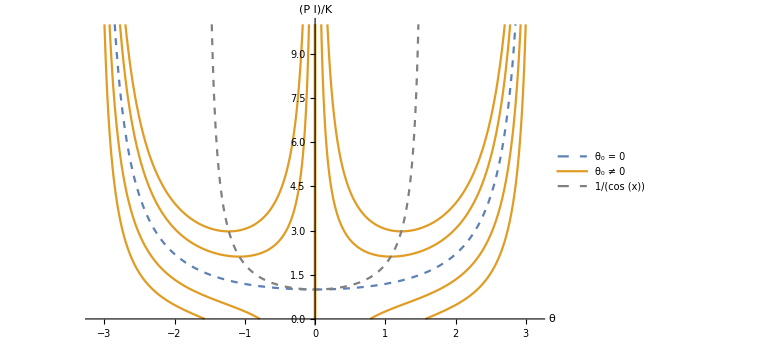

```mathematica
Manipulate[Show[{Plot3D[V[λ, θ, θ0], {λ, 0, 2}, {θ, -Pi, Pi}, AxesLabel->{"(P l)/K","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
ParametricPlot3D[{θ/Sin[θ],θ,V[θ/Sin[θ],θ, 0]},{θ,-π,π}],
ParametricPlot3D[{(θ-θ0)/Sin[θ],θ,V[(θ-θ0)/Sin[θ],θ, θ0]},{θ,-π,π}],ParametricPlot3D[{λ,0,V[λ,0, θ0]},{λ,0,2}]}, ImageSize->Large],
 {{θ0, 0}, -Pi, Pi, Pi/16}]

Manipulate[Plot[{ θ/Sin[θ],(θ-θ0)/Sin[θ],1/Cos[θ]}, {θ, -Pi, Pi}, PlotStyle->{{Dashed},{},{Gray, Dashed}}, PlotRange->{Automatic, {0,10}}, AxesLabel->{"θ", "(P l)/K"},LabelStyle->18, PlotLegends->{"θ_0 = 0", "θ_0 ≠ 0", "1/(cos (x))"}, ImageSize->Large], {{θ0, 0}, -Pi, Pi, Pi/16}, ContentSize->{800, 480}]

Plot[{ θ/Sin[θ],(θ-θ0)/Sin[θ]/.θ0 -> {-Pi/2, -Pi/4, Pi/4, Pi/2},1/Cos[θ]}, {θ, -Pi, Pi}, PlotStyle->{{Dashed},{},{Gray, Dashed}}, PlotRange->{Automatic, {0,10}}, AxesLabel->{"θ", "(P l)/K"},LabelStyle->18, PlotLegends->{"θ_0 = 0", "θ_0 ≠ 0", "1/(cos (x))"}, ImageSize->Large]
```

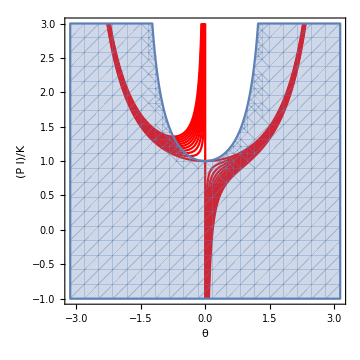

```mathematica
Show[
Table[ContourPlot[dV[λ,θ,θ0]==0, {θ, -Pi, Pi}, {λ, -1, 3}, ContourStyle->Red, PlotPoints->50, FrameLabel->{"θ", "(P l)/K"}, LabelStyle->18],
{θ0, 0, 10 Degree, 1 Degree}],
RegionPlot[d2V[λ, θ,θ0]>0, {θ, -Pi,Pi}, {λ, -1, 3}, Axes->True, Ticks->{Table[k*Pi, {k, -1, 1, 1/4}], Automatic}, GridLines->None],
 ImageSize->Medium
]
```

## Imperfezione di eccentricità e

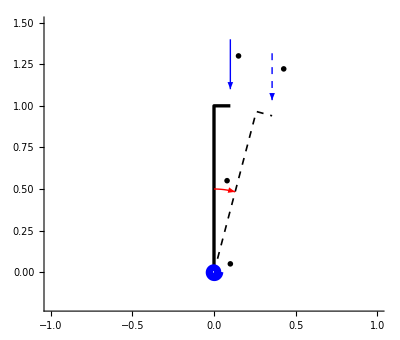

```mathematica
l=1;

carh=Graphics[Triangle[{{-1/2,-1},{0,0},{1/2,-1}}]];
cer=Graphics[{FaceForm[White],EdgeForm[Directive[Thick]],Disk[{0,0},1]}];
myCircle[o_,r_,{a_,b_},res_]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];
rspring[centre_,rounds_,radius_]:=Module[{},
x[t_]:=radius/rounds/(2*Pi)*t*Cos[t];
y[t_]:=radius/rounds/(2*Pi)*t*Sin[t];
ParametricPlot[{centre[[1]]+x[t],centre[[2]]+y[t]},{t,0,rounds*2*Pi},PlotStyle->Blue]
];

Show[{
Graphics[{Thickness[0.006],Line[{{0,0},{l*Sin[θ],l*Cos[θ]},{l*Sin[θ]+e*Cos[θ],l*Cos[θ]-e*Sin[θ]}}/.θ->0 Degree/.e->.1]}],
Graphics[{Thickness[0.003],Dashed,Line[{{0,0},{l*Sin[θ],l*Cos[θ]},{l*Sin[θ]+e*Cos[θ],l*Cos[θ]-e*Sin[θ]}}/.θ->15 Degree/.e->.1]}],
Graphics[{Inset[cer,{0,0},{0,0},0.05]}],
rspring[{0,0},4,0.05],
Graphics[Text[MaTeX["\\textcolor{blue}{K}",Magnification->2],{0.1,0.05}*l]],
Graphics[{Thick,Blue,Arrow[{{l*Sin[θ]+e*Cos[θ],1.4(l*Cos[θ]-e*Sin[θ])},{l*Sin[θ]+e*Cos[θ],1.1(l*Cos[θ]-e*Sin[θ])}}/.θ->0 Degree/.e->.1]}],
Graphics[Text[MaTeX["\\textcolor{blue}{P}",Magnification->2],{1.5(l*Sin[θ]+e*Cos[θ]),1.3(l*Cos[θ]-e*Sin[θ])}/.θ->0 Degree/.e->.1]],
Graphics[{Thick,Dashed,Blue,Arrow[{{l*Sin[θ]+e*Cos[θ],1.4(l*Cos[θ]-e*Sin[θ])},{l*Sin[θ]+e*Cos[θ],1.1(l*Cos[θ]-e*Sin[θ])}}/.θ->15Degree/.e->.1]}],
Graphics[Text[MaTeX["\\textcolor{blue}{P}",Magnification->2],{1.2(l*Sin[θ]+e*Cos[θ]),1.3(l*Cos[θ]-e*Sin[θ])}/.θ->15Degree/.e->.1]],
(*Graphics[{FaceForm[Black],EdgeForm[Directive[Thick]],Disk[{l*Sin[θ],l*Cos[θ]}/.θ->0 Degree,0.025]}],
Graphics[{FaceForm[Black],EdgeForm[Directive[Thick]],Disk[{l*Sin[θ],l*Cos[θ]}/.θ->15 Degree,0.025]}],*)
(*Graphics[Text[MaTeX["m",Magnification->2],{l*Sin[θ]+.1,1.05*l*Cos[θ]}/.θ->0 Degree]],*)
Graphics[{Red,Thick,Arrowheads[0.03],myCircle[{0,0},0.5*l,{90 Degree,75 Degree},10]}],
Graphics[Text[MaTeX["\\textcolor{red}{\\theta}",Magnification->2],{0.08,0.55}*l]]
},
PlotRange->{{-l,l},{-0.2*l,1.5*l}},
Axes->True,
ImageSize->{Automatic,500}]
```

```mathematica
ClearAll[θ, Ε, W, V, dV, λ, e, λ0, λ1, d2V]; (* e = a/l *)
Ε[θ_]:= 1/2(θ)^2;
W[λ_,θ_, e_]:= λ*(1- Cos[θ] + e*Sin[θ])
V[λ_,θ_, e_]:= Ε[θ] - W[λ,θ, e]
V[λ,θ, e]

dV[λ_,θ_, e_]:= D[V[λ,θ, e], θ]
dV[λ,θ, e]
λ0= λ/.Solve[dV[λ, θ, e] == 0, λ][[1]]

d2V[λ_,θ_, e_]:= D[dV[λ,θ, e], θ]
d2V[λ,θ, e]

λ1 = λ/.Solve[d2V[λ, θ, e]==0, λ][[1]]
```

θ^2/2-λ (1-Cos[θ]+e Sin[θ])

θ-λ (e Cos[θ]+Sin[θ])

θ/(e Cos[θ]+Sin[θ])

1-λ (Cos[θ]-e Sin[θ])

1/(Cos[θ]-e Sin[θ])

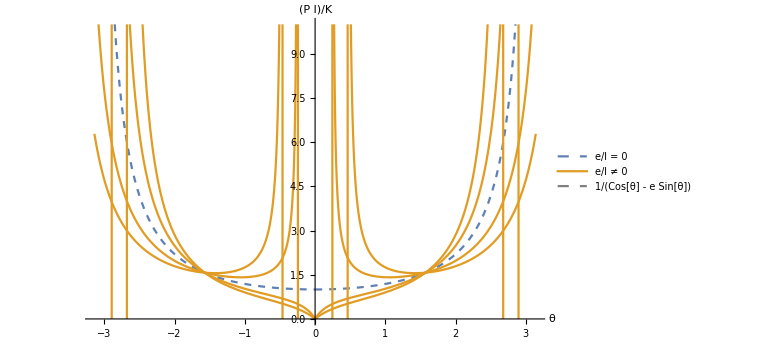

```mathematica
Manipulate[Show[{Plot3D[V[λ, θ, e], {λ, 0, 2}, {θ, -Pi, Pi}, AxesLabel->{"(P l)/K","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
(*ParametricPlot3D[{θ/Sin[θ],θ,V[θ/Sin[θ],θ, 0]},{θ,-π,π}],*)
ParametricPlot3D[{θ/(e Cos[θ]+Sin[θ]),θ,V[θ/(e Cos[θ]+Sin[θ]),θ, e]},{θ,-π,π}],
ParametricPlot3D[{λ,0,V[λ,0, e]},{λ,0,2}]}, 
ImageSize->Large],
 {{e, 0}, -1, 1, .1}]

Manipulate[Plot[{ θ/Sin[θ],θ/(e Cos[θ]+Sin[θ]),1/(Cos[θ]-e Sin[θ])}, {θ, -Pi, Pi}, PlotStyle->{{Dashed},{},{Gray, Dashed}}, PlotRange->{Automatic, {0,10}}, AxesLabel->{"θ", "(P l)/K"},LabelStyle->18, PlotLegends->{"e/l = 0", "e/l ≠ 0", "1/(Cos[θ] - e Sin[θ])"}, ImageSize->Large], {{e, 0}, -1, 1, 1/10}, ContentSize->{800, 480}]

Plot[{ θ/Sin[θ],θ/(e Cos[θ]+Sin[θ])/.e -> {-1/2, -1/4, 1/4, 1/2},1/(Cos[θ]-e Sin[θ])}, {θ, -Pi, Pi}, PlotStyle->{{Dashed},{},{Gray, Dashed}}, PlotRange->{Automatic, {0,10}}, AxesLabel->{"θ", "(P l)/K"},LabelStyle->18, PlotLegends->{"e/l = 0", "e/l ≠ 0", "1/(Cos[θ] - e Sin[θ])"}, ImageSize->Large]
```

## Unstable symmetrical post-critical system

## Sistema perfetto

```mathematica
ClearAll[θ, Ε, W, V, dV, λ];
Ε[θ_]:= 1/2 Sin[θ]^2;
W[λ_,θ_]:= λ*(1-Cos[θ]);
V[λ_,θ_]:= Ε[θ] - W[λ,θ]
V[λ,θ]

dV[λ_,θ_]:= D[V[λ,θ], θ]
dV[λ,θ]
λ0 = λ/.Solve[dV[λ, θ] == 0, λ][[1]]
```

-λ (1-Cos[θ])+Sin[θ]^2/2

-λ Sin[θ]+Cos[θ] Sin[θ]

Cos[θ]

-Graphics3D-

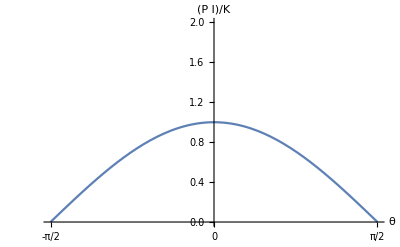

```mathematica
Show[Plot3D[V[λ, θ], {λ, 0, 2}, {θ, -Pi, Pi}, AxesLabel->{"(P l)/K","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
ParametricPlot3D[{Cos[θ],θ,V[Cos[θ],θ]},{θ,-π,π}],ParametricPlot3D[{λ,0,V[λ,0]},{λ,0,2}], ImageSize->Large]

Plot[{Cos[θ]}, {θ, -Pi/2, Pi/2}, PlotRange->{Automatic, {0,2}},   Ticks->{{-Pi,-3/4 Pi,-Pi/2, -Pi/4, 0, Pi/4, Pi/2, 3/4 Pi, Pi},Automatic}, AxesLabel->{"θ", "(P l)/K"},LabelStyle->18]
```

```mathematica
ClearAll[d2V]
d2V[λ_, θ_]:= D[dV[λ, θ], θ]
d2V[λ, θ]/.λ->λ0
```

-Sin[θ]^2

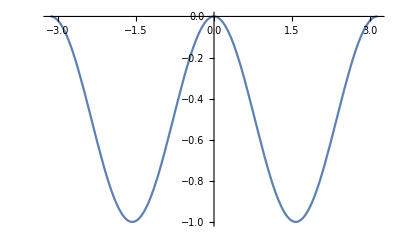

```mathematica
Plot[-Sin[θ]^2, {θ, -Pi, Pi}]
```

## Imperfezione di rotazione iniziale θ_0

```mathematica
ClearAll[θ, Ε, W, V, dV, λ, θ0, λ0, λ1];
Ε[θ_, θ0_]:= 1/2(Sin[θ]-Sin[θ0])^2;
W[λ_,θ_, θ0_]:= λ*(Cos[θ0]-Cos[θ]);
V[λ_,θ_, θ0_]:= Ε[θ, θ0] - W[λ,θ, θ0]
V[λ,θ, θ0]



dV[λ_,θ_, θ0_]:= D[V[λ,θ, θ0], θ]
dV[λ,θ, θ0]
λ0= λ/.Solve[dV[λ, θ, θ0] == 0, λ][[1]]

d2V[λ_, θ_, θ0_] := D[dV[λ, θ, θ0], θ]
d2V[λ, θ, θ0]//FullSimplify
λ1 = λ/.Solve[d2V[λ, θ, θ0]==0, λ][[1]]
```

-λ (-Cos[θ]+Cos[θ0])+1/2 (Sin[θ]-Sin[θ0])^2

-λ Sin[θ]+Cos[θ] (Sin[θ]-Sin[θ0])

Cot[θ] (Sin[θ]-Sin[θ0])

-λ Cos[θ]+Cos[θ]^2+Sin[θ] (-Sin[θ]+Sin[θ0])

Cos[θ]-Sin[θ] Tan[θ]+Sin[θ0] Tan[θ]

```mathematica
Manipulate[Show[{Plot3D[V[λ, θ, θ0], {λ, 0, 2}, {θ, -Pi, Pi}, AxesLabel->{"(P l)/K","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
ParametricPlot3D[{Cos[θ],θ,V[Cos[θ],θ, 0]},{θ,-π,π}],
ParametricPlot3D[{(Sin[θ]-Sin[θ0])/Tan[θ],θ,V[(Sin[θ]-Sin[θ0])/Tan[θ],θ, θ0]},{θ,-π,π}],ParametricPlot3D[{λ,0,V[λ,0, θ0]},{λ,0,2}]}, ImageSize->Large],
 {{θ0, 0}, -Pi, Pi, Pi/16}]

Manipulate[Plot[{Cos[θ],(Sin[θ]-Sin[θ0])/Tan[θ], (Cos[θ]^2 - Sin[θ]^2 + Sin[θ]*Sin[θ0])/Cos[θ]}, {θ, -π, π}, AxesLabel->{"θ", "(P l)/k"}, LabelStyle->18,Ticks->{{-π/2, 0, π/8, π/4, 3/8 π, π/2},Automatic}, PlotRange->Automatic, PlotStyle->{{Dashed},Automatic, {Gray, Thin}},PlotLegends->{"Cos[θ]", "(Sin[θ] - Sin[θ0])/Tan[θ]", "Stabilty transition"},  ImageSize->Large],
 {{θ0,0}, -π/2, π/2, π/16}]
```

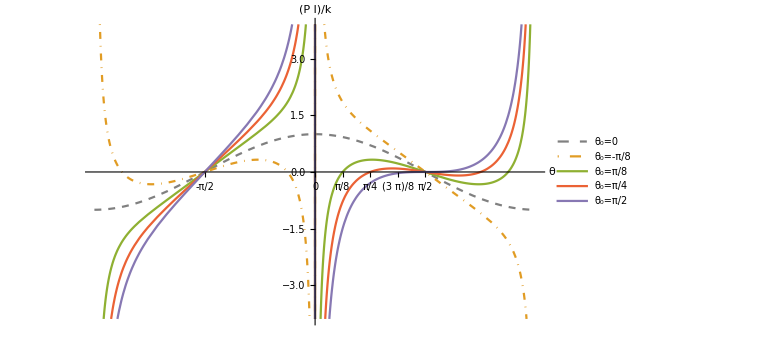

```mathematica
θ0=.
Plot[{Cos[θ],(Sin[θ]-Sin[θ0])/Tan[θ]/.θ0->-π/8,(Sin[θ]-Sin[θ0])/Tan[θ]/.θ0->π/8 ,(Sin[θ]-Sin[θ0])/Tan[θ]/.θ0->π/4  ,(Sin[θ]-Sin[θ0])/Tan[θ]/.θ0->π/2 }, {θ, -π, π}, AxesLabel->{"θ", "(P l)/k"},LabelStyle->18, Ticks->{{-π/2, 0, π/8, π/4, 3/8 π, π/2},Automatic}, PlotRange->Automatic, PlotStyle->{{Gray, Dashed},{Automatic, DotDashed}, Automatic,Automatic, Automatic}, PlotLegends->{{"θ_0=0","θ_0=-π/8","θ_0=π/8","θ_0=π/4","θ_0=π/2"}},  ImageSize->Large]
```

### Andamento della θ_cr di transizione tra stabilità e instabilità in funzione di θ_0

```mathematica
D[λ0, θ] /. θ-> ArcSin[Sin[θ0]^(1/3)]//FullSimplify
```

0

```mathematica
Series[ArcSin[Sin[θ0]^(1/3)], {θ0,0, 2}]
```

θ0^(1/3)+θ0/6+(3 θ0^(5/3))/40+O[θ0]^(7/3)

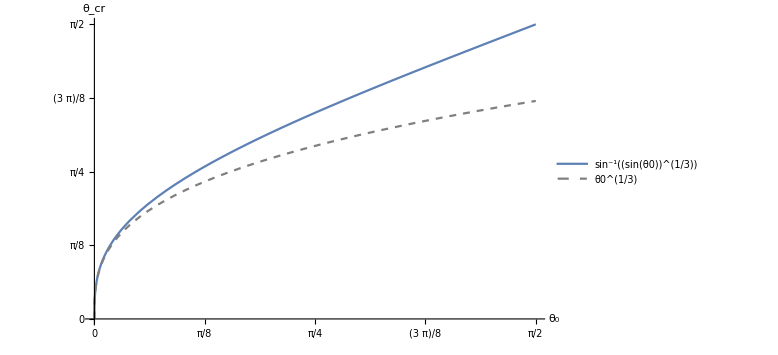

```mathematica
Plot[{ArcSin[Sin[θ0]^(1/3)], θ0^(1/3)}, {θ0, 0, π/2}, PlotStyle->{Automatic, {Gray, Dashed}}, PlotLegends->"Expressions",AxesLabel->{"θ_0", "θ_cr"},LabelStyle->18, Ticks->{{0, π/8, π/4, 3/8 π, π/2},{0, π/8, π/4, 3/8 π, π/2}}, ImageSize->Large]
```

### Andamento del carico massimo adimensionale in funzione di θ_0

```mathematica
λ0 /. θ -> ArcSin[Sin[θ0]^(1/3)] //FullSimplify (* Subscript[P, max]/kl *)
```

(1-Sin[θ0]^(2/3))^(3/2)

```mathematica
Series[λ0 /. θ -> ArcSin[Sin[θ0]^(1/3)] //FullSimplify, {θ0, 0, 2}]
```

1-(3 θ0^(2/3))/2+(3 θ0^(4/3))/8+θ0^2/16+O[θ0]^(8/3)

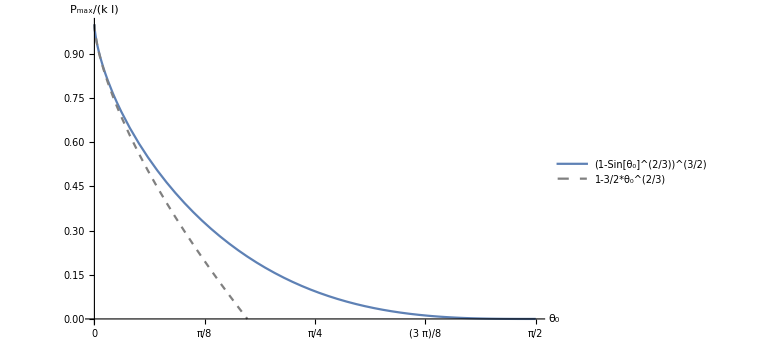

```mathematica
Plot[{(Sin[θ]-Sin[θ0])/Tan[θ] /.θ-> ArcSin[Sin[θ0]^(1/3)],1-3/2*θ0^(2/3)}, {θ0, 0, π/2}, PlotLegends->{"(1-Sin[θ_0]^(2/3))^(3/2)","1-3/2*θ_0^(2/3)" },PlotStyle->{Automatic, {Gray, Dashed}}, AxesLabel->{"θ_0", "P_max/(k l)"},LabelStyle->18,PlotRange->{Automatic, {0,1}} ,Ticks->{{0, π/8, π/4, 3/8 π, π/2},Automatic}, ImageSize->Large]
```

## Imperfezione di eccentricità “e”

```mathematica
ClearAll[θ, Ε, W, V, dV, λ, e, λ0, λ1, d2V]; (* e = a/l *)
Ε[θ_]:= 1/2(Sin[θ])^2;
W[λ_,θ_, e_]:= λ*(1- Cos[θ] + e*Sin[θ])
V[λ_,θ_, e_]:= Ε[θ] - W[λ,θ, e]
V[λ,θ, e]

dV[λ_,θ_, e_]:= D[V[λ,θ, e], θ]
dV[λ,θ, e]
λ0= λ/.Solve[dV[λ, θ, e] == 0, λ][[1]]

d2V[λ_,θ_, e_]:= D[dV[λ,θ, e], θ]
d2V[λ,θ, e]

λ1 = λ/.Solve[d2V[λ, θ, e]==0, λ][[1]]
```

Sin[θ]^2/2-λ (1-Cos[θ]+e Sin[θ])

Cos[θ] Sin[θ]-λ (e Cos[θ]+Sin[θ])

(Cos[θ] Sin[θ])/(e Cos[θ]+Sin[θ])

Cos[θ]^2-Sin[θ]^2-λ (Cos[θ]-e Sin[θ])

(Cos[θ]^2-Sin[θ]^2)/(Cos[θ]-e Sin[θ])

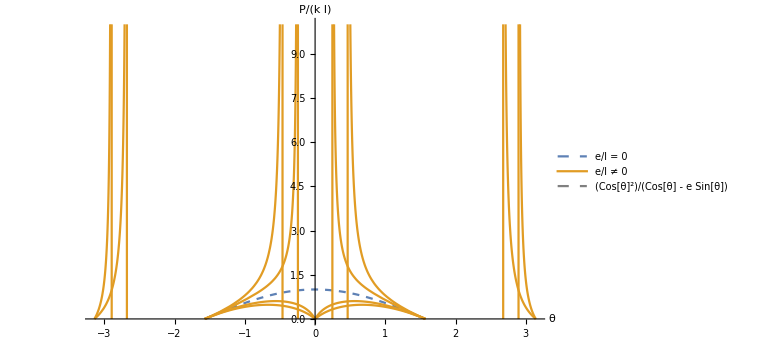

```mathematica
Manipulate[Show[{Plot3D[V[λ, θ, e], {λ, 0, 2}, {θ, -Pi, Pi}, AxesLabel->{"P/(k l)","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
(*ParametricPlot3D[{θ/Sin[θ],θ,V[θ/Sin[θ],θ, 0]},{θ,-π,π}],*)
ParametricPlot3D[{(Sin[θ] *Cos[θ])/(e Cos[θ]+Sin[θ]),θ,V[(Sin[θ] *Cos[θ])/(e Cos[θ]+Sin[θ]),θ, e]},{θ,-π,π}],
ParametricPlot3D[{λ,0,V[λ,0, e]},{λ,0,2}]}, 
ImageSize->Large],
 {{e, 0}, -1, 1, .1}]

Manipulate[Plot[{ Cos[θ],(Sin[θ] *Cos[θ])/(e Cos[θ]+Sin[θ]),(Cos[θ]^2 - Sin[θ]^2)/(Cos[θ]-e Sin[θ])}, {θ, -Pi, Pi}, PlotStyle->{{Dashed},{},{Gray, Dashed}}, PlotRange->{Automatic, {0,10}}, AxesLabel->{"θ", "P/(k l)"},LabelStyle->18, PlotLegends->{"e/l = 0", "e/l ≠ 0", "Cos[θ]^2/(Cos[θ] - e Sin[θ])"}, ImageSize->Large], {{e, 0}, -1, 1, 1/10}, ContentSize->{800, 480}]

Plot[{ Cos[θ],(Sin[θ] *Cos[θ])/(e Cos[θ]+Sin[θ])/.e -> {-1/2, -1/4, 1/4, 1/2},(Cos[θ]^2 - Sin[θ]^2)/(Cos[θ]-e Sin[θ])}, {θ, -Pi, Pi}, PlotStyle->{{Dashed},{},{Gray, Dashed}}, PlotRange->{Automatic, {0,10}}, AxesLabel->{"θ", "P/(k l)"},LabelStyle->18, PlotLegends->{"e/l = 0", "e/l ≠ 0", "Cos[θ]^2/(Cos[θ] - e Sin[θ])"}, ImageSize->Large]
```

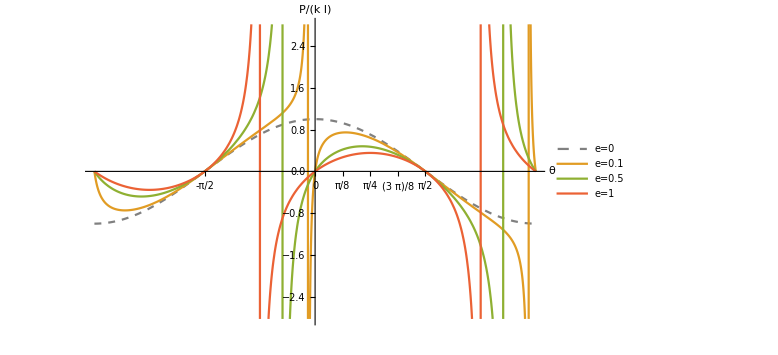

```mathematica
Plot[{Cos[θ],Cos[θ]/(1+e/Tan[θ])/.e->.1 ,Cos[θ]/(1+e/Tan[θ])/.e->.5 ,Cos[θ]/(1+e/Tan[θ])/.e->1 }, {θ, -π, π}, AxesLabel->{"θ", "P/(k l)"},LabelStyle->18, Ticks->{{-π/2, 0, π/8, π/4, 3/8 π, π/2},Automatic}, PlotRange->Automatic, PlotStyle->{{Gray, Dashed},Automatic,Automatic, Automatic}, PlotLegends->{{"e=0","e=0.1","e=0.5", "e=1"}}, ImageSize->Large]
```

### Andamento della θ_cr di transizione tra stabilità e instabilità in funzione di e/l

```mathematica
d2V[λ, θ, e]/.λ->λ0//Simplify
```

(e Cos[θ]^3-Sin[θ]^3)/(e Cos[θ]+Sin[θ])

```mathematica
d2V[λ, θ, e] /. λ->λ0 /. e -> Tan[θ]^3 //Simplify
```

0

```mathematica
Series[ArcTan[e^(1/3)], {e,0,2}]
```

e^(1/3)-e/3+e^(5/3)/5+O[e]^(7/3)

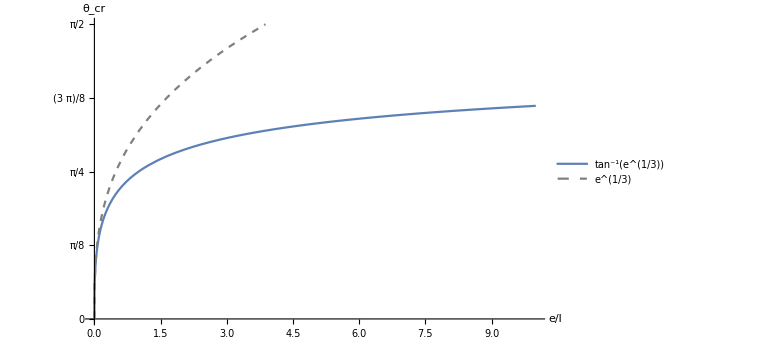

```mathematica
Plot[{ArcTan[(e)^(1/3)], e^(1/3)}, {e, 0, 10}, PlotLegends->"Expressions",PlotStyle->{Automatic, {Gray, Dashed}},AxesLabel->{"e/l", "θ_cr"}, LabelStyle->18,Ticks->{Automatic,{0, π/8, π/4, 3/8 π, Pi/2}}, PlotRange->{Automatic, π/2}, ImageSize->Large]
```

### Andamento del carico massimo adimensionale in funzione di e/l

```mathematica
D[λ0, θ]//Simplify
```

(e Cos[θ]^3-Sin[θ]^3)/(e Cos[θ]+Sin[θ])^2

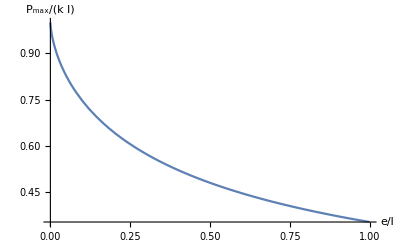

```mathematica
Plot[{λ0/.θ->ArcTan[e^(1/3)]}, {e, 0, 1}, AxesLabel->{"e/l", "P_max/(k l)"},LabelStyle->18, Ticks->{Automatic,Automatic}, PlotRange->Automatic]
```

## Asymmetrical post-critical system

## Sistema perfetto

```mathematica
ClearAll[θ, Ε, W, V, dV, λ];
Ε[θ_]:= 1/2*2*(Sqrt[1+Sin[θ]] - 1)^2;
W[λ_,θ_]:= λ*(1-Cos[θ]);
V[λ_,θ_]:= Ε[θ] - W[λ,θ]
V[λ,θ]

dV[λ_,θ_]:= D[V[λ,θ], θ]
dV[λ,θ]
λ0 = λ/.Solve[dV[λ, θ] == 0, λ][[1]]
```

-λ (1-Cos[θ])+(-1+√(1+Sin[θ]))^2

-λ Sin[θ]+(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]))

(Cot[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]))

```mathematica
Show[Plot3D[V[λ, θ], {λ, 0, 2}, {θ, -1.2Pi, 1.2 Pi}, AxesLabel->{"(P l)/K","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
ParametricPlot3D[{(Cot[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ])),θ,V[(Cot[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ])),θ]},{θ,-π,π}],ParametricPlot3D[{λ,0,V[λ,0]},{λ,-2,2}], ParametricPlot3D[{λ,-Pi,V[λ,-Pi]},{λ,-2,2}],ParametricPlot3D[{λ,Pi,V[λ,Pi]},{λ,-2,2}], ImageSize->Large]
```

-Graphics3D-

```mathematica
Limit[λ0, θ->-Pi/1.9999]//FullSimplify
```

-1.41414

```mathematica
Sqrt[2]//N
```

1.41421

```mathematica
Solve[Limit[dV[λ, θ], θ-> -Pi/2, Direction->1]==0, λ]
Solve[Limit[dV[λ, θ], θ-> -Pi/2, Direction->-1]==0, λ]
```

{{λ→-√2}}

{{λ→√2}}

```mathematica
Limit[λ0, θ->Pi]
```

-1/2

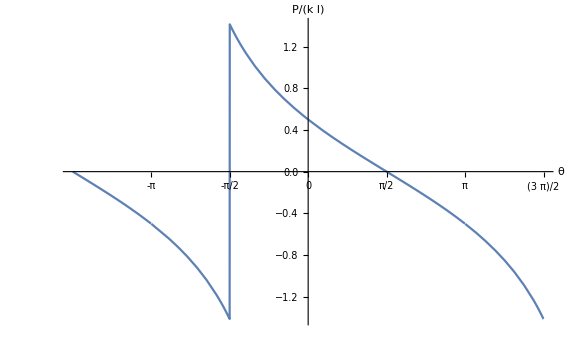

```mathematica
Plot[(Sqrt[1+Sin[θ]]-1)/(Tan[θ]*Sqrt[1+Sin[θ]]), {θ, -3/2π, 3/2 π}, Ticks->{{-π, -π/2, 0, π/2, π, 3/2 π}, Automatic},AxesLabel->{"θ","P/(k l)"}, LabelStyle->18, ImageSize->Large]
```

```mathematica
ClearAll[d2V]
d2V[λ_, θ_]:= D[dV[λ, θ], θ]
d2V[λ, θ]//FullSimplify
d2V[λ, θ]/.θ->0//FullSimplify
d2V[λ, θ]/.λ->λ0 //FullSimplify
```

1/2 (-2 λ Cos[θ]-2 Sin[θ]+√(1+Sin[θ]))

1/2-λ

(2+Csc[θ] (3+Cos[2 θ]-4 √(1+Sin[θ])))/(4 √(1+Sin[θ]))

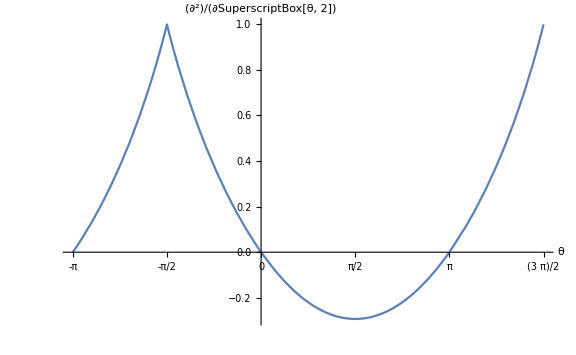

```mathematica
Plot[(2+Csc[θ] (3+Cos[2 θ]-4 √(1+Sin[θ])))/(4 √(1+Sin[θ])), {θ, -π, 3 π/2}, Ticks->{{-π, -π/2, 0, π/2, π, 3/2 π}, Automatic},AxesLabel->{"θ","∂^2/(∂SuperscriptBox[θ, 2])"},LabelStyle->18,  ImageSize->Large]
```

```mathematica
D[d2V[λ, θ], θ]/.θ->0
```

-3/4

## Imperfezione di rotazione iniziale θ_0

```mathematica
ClearAll[θ, Ε, W, V, dV, λ, θ0, λ0, λ1];
Ε[θ_, θ0_]:= (Sqrt[1+Sin[θ]]-Sqrt[1+Sin[θ0]])^2;
W[λ_,θ_, θ0_]:= λ*(Cos[θ0]-Cos[θ]);
V[λ_,θ_, θ0_]:= Ε[θ, θ0] - W[λ,θ, θ0]
V[λ,θ, θ0]



dV[λ_,θ_, θ0_]:= D[V[λ,θ, θ0], θ]
dV[λ,θ, θ0]
λ0= λ/.Solve[dV[λ, θ, θ0] == 0, λ][[1]]

d2V[λ_, θ_, θ0_] := D[dV[λ, θ, θ0], θ]
d2V[λ, θ, θ0]//FullSimplify
λ1 = λ/.Solve[d2V[λ, θ, θ0]==0, λ][[1]]//FullSimplify
```

-λ (-Cos[θ]+Cos[θ0])+(√(1+Sin[θ])-√(1+Sin[θ0]))^2

-λ Sin[θ]+(Cos[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ]))

(Cot[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ]))

-λ Cos[θ]-Sin[θ]+1/2 √(1+Sin[θ]) √(1+Sin[θ0])

((Cos[θ/2]+Sin[θ/2]) (√(1+Sin[θ0])+Sin[θ] (-2 √(1+Sin[θ])+√(1+Sin[θ0]))))/(2 (Cos[θ/2]-Sin[θ/2]) (1+Sin[θ])^(3/2))

```mathematica
Manipulate[Show[{Plot3D[V[λ, θ, θ0], {λ, 0, 2}, {θ, -Pi, Pi}, AxesLabel->{"P/(k l)","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
ParametricPlot3D[{(Cot[θ] (√(1+Sin[θ])-1))/(√(1+Sin[θ])),θ,V[(Cot[θ] (√(1+Sin[θ])-1))/(√(1+Sin[θ])),θ, 0]},{θ,-π,π}],
ParametricPlot3D[{(Cot[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ])),θ,V[(Cot[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ])),θ, θ0]},{θ,-π,π}],ParametricPlot3D[{λ,0,V[λ,0, θ0]},{λ,0,2}]}, ImageSize->Large],
 {{θ0, 0}, -Pi, Pi, Pi/16}]

Manipulate[Plot[{(Cot[θ] (√(1+Sin[θ])-1))/(√(1+Sin[θ])),(Cot[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ])), ((Cos[θ/2]+Sin[θ/2]) (√(1+Sin[θ0])+Sin[θ] (-2 √(1+Sin[θ])+√(1+Sin[θ0]))))/(2 (Cos[θ/2]-Sin[θ/2]) (1+Sin[θ])^(3/2))}, {θ, -3/2π, 3/2π}, AxesLabel->{"θ", "(P l)/k"},LabelStyle->18, Ticks->{{-3/2 π,-π,-π/2, 0, π/2, π, 3/2 π},Automatic}, PlotRange->Automatic, PlotStyle->{{Dashed},Automatic, {Gray, Thin}},PlotLegends->{"(Cot[θ] (SqrtBox[1 + Sin[θ]] - 1))/(√(1 + Sin[θ]))", "(Cot[θ] (SqrtBox[1 + Sin[θ]] - SqrtBox[1 + Sin[θ0]]))/(√(1 + Sin[θ]))", "Stabilty transition"},  ImageSize->Large],
 {{θ0,0}, -π/2, π/2, π/16}]
```

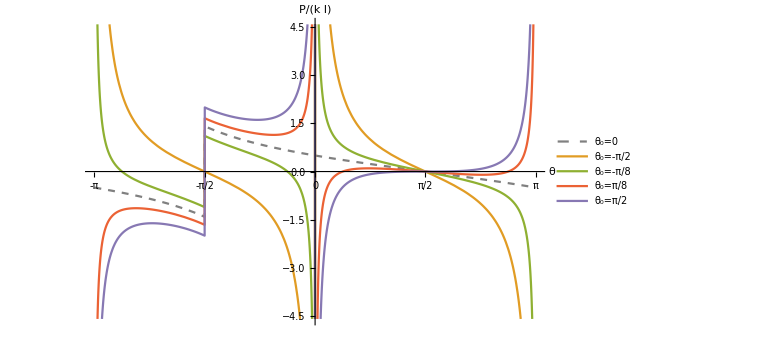

```mathematica
θ0=.
Plot[{(Cot[θ] (√(1+Sin[θ])-1))/(√(1+Sin[θ])),(Cot[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ]))/.θ0->-π/2,(Cot[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ]))/.θ0->-π/8,(Cot[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ]))/.θ0->π/8 ,(Cot[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ]))/.θ0->π/2 }, {θ, -π, π}, AxesLabel->{"θ", "P/(k l)"},LabelStyle->18, Ticks->{{ -π,-π/2, 0, π/2, Pi},Automatic}, PlotRange->Automatic, PlotStyle->{{Gray, Dashed},Automatic, Automatic,Automatic, Automatic}, PlotLegends->{{"θ_0=0","θ_0=-π/2","θ_0=-π/8","θ_0=π/8","θ_0=π/2"}},  ImageSize->Large]
```

### Andamento della θ_cr e di P_max in funzione di θ_0

```mathematica
λ0
```

(Cot[θ] (√(1+Sin[θ])-√(1+Sin[θ0])))/(√(1+Sin[θ]))

```mathematica
Series[Series[λ0, {θ0,0, 1}], {θ, 0, 1}]//Simplify
```

(1/2-(3 θ)/8+O[θ]^2)+(-1/(2 θ)+1/4-θ/48+O[θ]^2) θ0+O[θ0]^2

```mathematica
Solve[D[(1/2 - 3/8*θ) - (1/(2*θ)+1/4)*θ0, θ]==0, θ]
```

{{θ→-(2 √θ0)/(√3)},{θ→(2 √θ0)/(√3)}}

```mathematica
Series[λ0 /. θ-> 2*Sqrt[θ0]/Sqrt[3], {θ0, 0, 1}]
Series[λ0 /. θ-> -2*Sqrt[θ0]/Sqrt[3], {θ0, 0, 1}]
```

1/2-(√3 √θ0)/2+θ0/3+O[θ0]^(3/2)

1/2+(√3 √θ0)/2+θ0/3+O[θ0]^(3/2)

```mathematica
θ0=.;
θcr = .;
λcr = .;
θin = 0;
θfin = π/2;
step = 1/1000;
nel = (θfin - θin)/step;
θ1 = Table[θ0, {θ0, θin, θfin, step}];
```

```mathematica
θcr = Table[θ/.FindRoot[-2 √(1+Sin[θ])+2 √(1+Sin[θ0])+Sin[θ] (-2 √(1+Sin[θ])+2 √(1+Sin[θ0])+Cos[θ]^2 √(1+Sin[θ0])), {θ, π/4}], {θ0, θin, θfin, step}];
```

```mathematica
λcr = Table[λ0 /. θ->θcr[[i]] /. θ0 -> θ1[[i]], {i, 1, nel}];
```

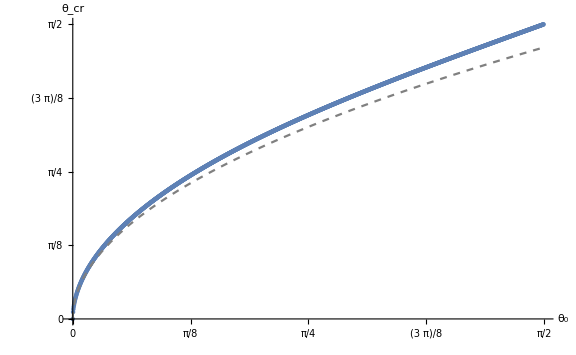

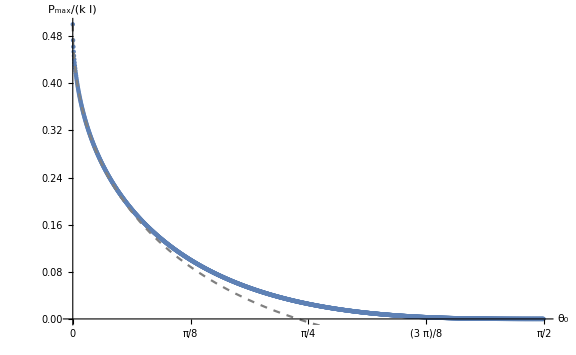

```mathematica
Show[ListPlot[Table[{θ1[[i]], θcr[[i]]}, {i, 1, nel}],
Ticks->{Table[k*Pi, {k, 0, 1/2, 1/16}], Table[k*Pi, {k, 0, 1/2, 1/16}]},
AxesLabel->{"θ_0", "θ_cr"},LabelStyle->18,
ImageSize->Large],
Plot[(2 √θ0)/(√3), {θ0, 0, π/2}, PlotStyle->{Gray, Dashed}]]
Show[ListPlot[Table[{θ1[[i]], λcr[[i]]}, {i, 1, nel}],
Ticks->{Table[k*Pi, {k, 0, 1/2, 1/16}], Automatic},
AxesLabel->{"θ_0", "P_max/(k l)"},LabelStyle->18,
ImageSize->Large],
Plot[1/2-(√3 √θ0)/2+θ0/3, {θ0, 0, π/2}, PlotStyle->{Gray, Dashed}]]
```

```mathematica
ClearAll[θ, θ0]
d2V[λ, θ, θ0] /. λ->λ0 //FullSimplify
```

(Csc[θ] (-4 √(1+Sin[θ])+3 √(1+Sin[θ0])+(Cos[2 θ]+2 Sin[θ]) √(1+Sin[θ0])))/(4 √(1+Sin[θ]))

```mathematica
Manipulate[Plot[(Csc[θ] (-4 √(1+Sin[θ])+3 √(1+Sin[θ0])+(Cos[2 θ]+2 Sin[θ]) √(1+Sin[θ0])))/(4 √(1+Sin[θ])), {θ, -Pi, Pi}, ImageSize->Large, AxesLabel->{"θ", "∂^2/(∂SuperscriptBox[θ, 2])"}, LabelStyle->18,Ticks->{Table[k*Pi, {k, -1, 1, 1/8}], Automatic}], {θ0, 0, Pi, Pi/16}]
```

## Imperfezione di eccentricità “e”

```mathematica
ClearAll[θ, Ε, W, V, dV, λ, e, λ0, λ1, d2V]; (* e = a/l *)
Ε[θ_]:= (Sqrt[1+Sin[θ]] - 1)^2;
W[λ_,θ_, e_]:= λ*(1- Cos[θ] + e*Sin[θ])
V[λ_,θ_, e_]:= Ε[θ] - W[λ,θ, e]
V[λ,θ, e]

dV[λ_,θ_, e_]:= D[V[λ,θ, e], θ]
dV[λ,θ, e]
λ0= λ/.Solve[dV[λ, θ, e] == 0, λ][[1]]

d2V[λ_,θ_, e_]:= D[dV[λ,θ, e], θ]
d2V[λ,θ, e]//FullSimplify

λ1 = λ/.Solve[d2V[λ, θ, e]==0, λ][[1]]//Simplify
```

-λ (1-Cos[θ]+e Sin[θ])+(-1+√(1+Sin[θ]))^2

-λ (e Cos[θ]+Sin[θ])+(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]))

(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]) (e Cos[θ]+Sin[θ]))

-λ Cos[θ]+(-1+e λ) Sin[θ]+1/2 √(1+Sin[θ])

((Cos[θ/2]+Sin[θ/2])^2 (-1+Sin[θ] (-1+2 √(1+Sin[θ]))))/(2 (1+Sin[θ])^(3/2) (-Cos[θ]+e Sin[θ]))

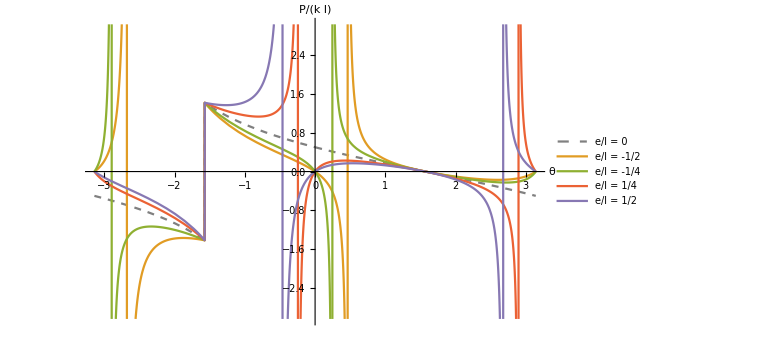

```mathematica
Manipulate[Show[{Plot3D[V[λ, θ, e], {λ, 0, 2}, {θ, -Pi, Pi}, AxesLabel->{"P/(k l)","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
ParametricPlot3D[{(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]) (e Cos[θ]+Sin[θ])),θ,V[(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]) (e Cos[θ]+Sin[θ])),θ, e]},{θ,-π,π}],
ParametricPlot3D[{λ,0,V[λ,0, e]},{λ,0,2}]}, 
ImageSize->Large],
 {{e, 0}, -1, 1, .1}]

Manipulate[Plot[{ (Cot[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ])),(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]) (e Cos[θ]+Sin[θ])), ((Cos[θ/2]+Sin[θ/2])^2 (-1+Sin[θ] (-1+2 √(1+Sin[θ]))))/(2 (1+Sin[θ])^(3/2) (-Cos[θ]+e Sin[θ]))}, {θ, -Pi, Pi}, PlotStyle->{{Dashed},{},{Gray, Thin}}, PlotRange->{Automatic, Automatic}, AxesLabel->{"θ", "P/(k l)"},LabelStyle->18, PlotLegends->{"e/l = 0", "e/l ≠ 0","Stability transition"}, ImageSize->Large], {{e, 0}, -1, 1, 1/10}, ContentSize->{800, 480}]

Plot[{ (Cot[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ])),(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]) (e Cos[θ]+Sin[θ]))/.e -> -1/2,(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]) (e Cos[θ]+Sin[θ]))/.e -> -1/4,(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]) (e Cos[θ]+Sin[θ]))/.e -> 1/4,(Cos[θ] (-1+√(1+Sin[θ])))/(√(1+Sin[θ]) (e Cos[θ]+Sin[θ]))/.e -> 1/2}, {θ, -Pi, Pi}, PlotStyle->{{Dashed, Gray},{}, {},{},{}}, PlotRange->{Automatic, Automatic}, AxesLabel->{"θ", "P/(k l)"},LabelStyle->18, PlotLegends->{"e/l = 0", "e/l = -1/2","e/l = -1/4", "e/l = 1/4", "e/l = 1/2"}, ImageSize->Large]
```

### Andamento della θ_cr di transizione tra stabilità e instabilità in funzione di e/l

```mathematica
Solve[d2V[λ, θ, e]==0/.λ->λ0, θ]
```

$Aborted

```mathematica
e=.;
θcr = .;
λcr = .;
ein = 0;
efin = 1;
step = 1/1000;
nel = (efin - ein)/step;
e1 = Table[e, {e, ein, efin, step}];
```

```mathematica
Simplify[D[λ0, θ]]
```

-((Cos[θ/2]+Sin[θ/2])^2 (-3-2 e Cos[θ]-Cos[2 θ]-2 Sin[θ]+4 √(1+Sin[θ])+e Sin[2 θ]))/(4 (1+Sin[θ])^(3/2) (e Cos[θ]+Sin[θ])^2)

```mathematica
θcr = Table[θ/.FindRoot[(-3-2 e Cos[θ]-Cos[2 θ]-2 Sin[θ]+4 √(1+Sin[θ])+e Sin[2 θ]), {θ, π/4}], {e, ein, efin, step}];
```

```mathematica
Series[Series[λ0, {e, 0, 1}], {θ, 0, 1}]
```

(1/2-(3 θ)/8+O[θ]^2)+(-1/(2 θ)+3/8+(5 θ)/48+O[θ]^2) e+O[e]^2

```mathematica
Solve[D[1/2-(3 θ)/8 + (-1/(2 θ)+3/8+(5 θ)/48)*e, θ]==0, θ]
```

{{θ→-(2 √6 √e)/(√(18-5 e))},{θ→(2 √6 √e)/(√(18-5 e))}}

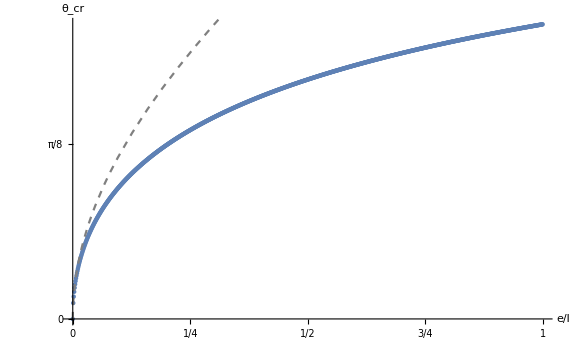

```mathematica
Show[ListPlot[Table[{e1[[i]], θcr[[i]]}, {i, 1, nel}],
Ticks->{Table[k, {k, 0, 1, 1/4}], Table[k*Pi, {k, 0, 1/2, 1/16}]},
AxesLabel->{"e/l", "θ_cr"},LabelStyle->18,
ImageSize->Large],
Plot[(2 √6 √e)/(√(18-5 e)), {e, 0, π/2}, PlotStyle->{Gray, Dashed}]]
```

### Andamento del carico massimo adimensionale in funzione di e/l

```mathematica
Series[λ0/.θ->-(2 √6 √e)/(√(18-5 e)), {e,0,1}]
```

1/2+(√3 √e)/2+(5 e)/6+O[e]^(3/2)

```mathematica
Series[λ0/.θ->+(2 √6 √e)/(√(18-5 e)), {e,0,1}]
```

1/2-(√3 √e)/2+(5 e)/6+O[e]^(3/2)

```mathematica
λcr = Table[λ0 /. θ->θcr[[i]] /. e -> e1[[i]], {i, 1, nel}];
```

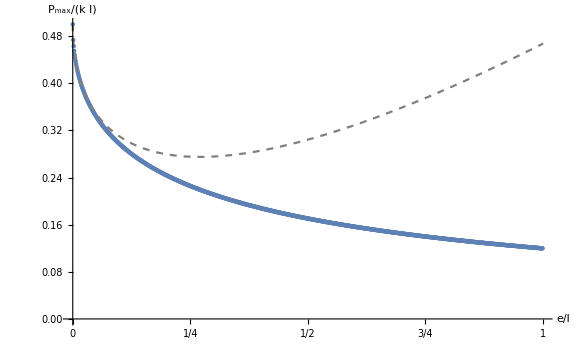

```mathematica
Show[ListPlot[Table[{e1[[i]], λcr[[i]]}, {i, 1, nel}],
Ticks->{Table[k, {k, 0, 1, 1/4}], Automatic},
AxesLabel->{"e/l", "P_max/(k l)"},LabelStyle->18,
ImageSize->Large],
Plot[1/2-(√3 √e)/2+(5 e)/6, {e, 0, 1}, PlotStyle->{Gray, Dashed}]]
```

```mathematica
Integrate[P/l*(Cos[a]*(s-l) + l), {s, 0, l}]//Simplify
```

-1/2 l P (-2+Cos[a])

```mathematica
Integrate[q*(l - Cos[a]*(l-s)), {s, 0, l}]
```

l^2 q-1/2 l^2 q Cos[a]

## Slave-load system

```mathematica
ClearAll[θ, Ε, W, V, dV, λ, λ0];
Ε[θ_]:= 1/2*θ^2;
W[λ_,θ_, d_]= λ*(Abs[1-d] - Sqrt[1+d^2 + 2*d*Cos[θ]]);
V[λ_,θ_, d_]= Ε[θ] - W[λ,θ, d]
V[λ,θ, d]

dV[λ_,θ_, d_]= D[V[λ,θ, d], θ]
dV[λ,θ, d]
λ0[θ_, d_] = λ/.Solve[dV[λ, θ, d] == 0, λ][[1]]
```

θ^2/2-λ (Abs[1-d]-√(1+d^2+2 d Cos[θ]))

θ^2/2-λ (Abs[1-d]-√(1+d^2+2 d Cos[θ]))

θ-(d λ Sin[θ])/(√(1+d^2+2 d Cos[θ]))

θ-(d λ Sin[θ])/(√(1+d^2+2 d Cos[θ]))

(θ √(1+d^2+2 d Cos[θ]) Csc[θ])/d

```mathematica
ClearAll[d2V]
d2V[λ_, θ_, d_]= D[dV[λ, θ, d], θ];
d2V[λ, θ, d]//FullSimplify
```

1-(d λ (Cos[θ] (1+d^2+2 d Cos[θ])+d Sin[θ]^2))/((1+d^2+2 d Cos[θ])^(3/2))

```mathematica
Manipulate[
Show[Plot3D[V[λ, θ, d], {λ, -2, 2}, {θ, -Pi, Pi}, AxesLabel->{"(P l)/K","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
ParametricPlot3D[{(θ √(1+d^2+2 d Cos[θ]) Csc[θ])/d,θ,V[(θ √(1+d^2+2 d Cos[θ]) Csc[θ])/d,θ, d]},{θ,-π,π}],ParametricPlot3D[{λ,0,V[λ,0, d]},{λ,-2,2}], ImageSize->Large], {d, -2, 2}]
```

```mathematica
Manipulate[Plot[λ0[θ, d], {θ, -Pi, Pi}, ImageSize->Large, AxesLabel->{"θ", "(P l)/K"},LabelStyle->18, Ticks->{Table[k*Pi, {k, -1, 1, 1/4}], Automatic}], {d, -10, 10, .5}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
dV[λ, θ, d]
```

θ-(d λ Sin[θ])/(√(1+d^2+2 d Cos[θ]))

```mathematica
d2V[λ, θ, d]//FullSimplify
```

1-(d λ (Cos[θ] (1+d^2+2 d Cos[θ])+d Sin[θ]^2))/((1+d^2+2 d Cos[θ])^(3/2))

```mathematica
Manipulate[Show[
ContourPlot[θ-(d λ Sin[θ])/(√(1+d^2+2 d Cos[θ]))==0, {θ, -Pi, Pi}, {λ, -2, 2},Axes->True,ContourStyle->Red,PlotPoints->50,FrameLabel->{"θ","(P l)/K"},LabelStyle->18],
Plot[1,{θ, -Pi, Pi}, PlotStyle->{Gray, Dashed}],
RegionPlot[1-(d λ (Cos[θ] (1+d^2+2 d Cos[θ])+d Sin[θ]^2))/((1+d^2+2 d Cos[θ])^(3/2))>0, {θ, -Pi, Pi}, {λ, -2, 2}, PlotPoints->50], ImageSize->Large],
{d, -2, 50, 1/2}]
```

```mathematica
Limit[λ0, θ->0]
```

(√((1+d)^2))/d

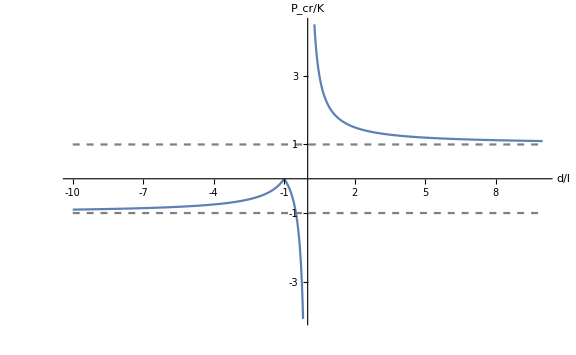

```mathematica
Show[
Plot[(√((1+d)^2))/d, {d, -10, 10}, AxesLabel-> {"d/l", "P_cr/K"},LabelStyle->18, ImageSize->Large, Ticks->{Table[k, {k, -10, 10, 1}], Table[k, {k,-5, 5, 2}]}], 
Plot[-1, {d, -10, 10}, PlotStyle->{Dashed, Gray}],
Plot[1, {d, -10, 10}, PlotStyle->{Dashed, Gray}]
]
```

```mathematica
d2V[λ, θ, d]
```

1-(d λ Cos[θ])/(√(1+d^2+2 d Cos[θ]))-(d^2 λ Sin[θ]^2)/((1+d^2+2 d Cos[θ])^(3/2))

```mathematica
ClearAll[λ1]
λ1[θ_, d_] = λ/.Solve[d2V[λ, θ, d] ==0, λ][[1]]
```

((1+d^2+2 d Cos[θ])^(3/2))/(d (Cos[θ]+d^2 Cos[θ]+2 d Cos[θ]^2+d Sin[θ]^2))

```mathematica
Manipulate[Plot[λ1[θ, d], {θ, -Pi, Pi}, ImageSize->Large, AxesLabel->{"θ", "∂^2/(∂SuperscriptBox[θ, 2])"},LabelStyle->18, Ticks->{Table[k*Pi, {k, -1, 1, 1/4}], Automatic}], {d, -2, 2, .1}]
```

## Snap-through

```mathematica
ClearAll[θ, Ε, W, V, dV,d2V, λ, θ0, λ0, λ1];
Ε[θ_, θ0_]= 1/4*(1/Cos[θ0]-1/Cos[θ])^2;
W[λ_,θ_, θ0_]= λ/2*(Tan[θ0]-Tan[θ]);
V[λ_,θ_, θ0_]= Ε[θ, θ0] - W[λ,θ, θ0]

dV[λ_,θ_, θ0_]= D[V[λ,θ, θ0], θ]
λ0[θ_, θ0_]= λ/.Solve[dV[λ, θ, θ0] == 0, λ][[1]]

d2V[λ_, θ_, θ0_] = D[dV[λ, θ, θ0], θ]
λ1[θ_, θ0_] = λ/.Solve[d2V[λ, θ, θ0]==0, λ][[1]]//FullSimplify
```

1/4 (-Sec[θ]+Sec[θ0])^2-1/2 λ (-Tan[θ]+Tan[θ0])

1/2 λ Sec[θ]^2-1/2 Sec[θ] (-Sec[θ]+Sec[θ0]) Tan[θ]

-((Sec[θ]-Sec[θ0]) Sin[θ])

-1/2 Sec[θ]^3 (-Sec[θ]+Sec[θ0])+λ Sec[θ]^2 Tan[θ]+1/2 Sec[θ]^2 Tan[θ]^2-1/2 Sec[θ] (-Sec[θ]+Sec[θ0]) Tan[θ]^2

1/2 (Csc[θ] (-Sec[θ]+Sec[θ0])+Sec[θ0] Sin[θ]-2 Tan[θ])

```mathematica
Manipulate[
Show[{
Plot3D[V[λ, θ, θ0], {λ, -2, 2}, {θ, -Pi, Pi}, AxesLabel->{"P/(k l)","θ","V"},LabelStyle->18,
Ticks->{Automatic,{-Pi/4,-Pi/2,-3Pi/4,-Pi,0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}],
ParametricPlot3D[{λ0[θ, θ0],θ,V[λ0[θ, θ0],θ, θ0]},{θ,-π,π}]
},
 ImageSize->Large],
 {{θ0, 0}, -Pi, Pi, Pi/16}]
```

```mathematica
(*Manipulate[
Plot[λ0[θ, θ0], {θ, -Pi, Pi},ImageSize->Large],
ContourPlot[ArcTan[1/Sec[θ0]^(1/3),-√(1-1/Sec[θ0]^(2/3))]
 {{θ0,0}, -Pi/2, Pi/2, Pi/16}]*)
```

-√(1-Cos[θ0]^(2/3)) (1/Cos[θ0]^(1/3)-Sec[θ0])

```mathematica
Manipulate[
Show[
RegionPlot[d2V[λ, θ, θ0]>0, {θ, -Pi, Pi}, {λ, -2, 2}, FrameLabel->{"θ", "P/(k l)"},LabelStyle->18, Axes->True],
ContourPlot[dV[λ, θ, θ0] == 0, {θ, -Pi, Pi}, {λ, -2, 2}, ContourStyle->Red],
Graphics[{PointSize[Large],Pink,Point[{ArcCos[Cos[θ0]^(1/3)],λ0[ArcCos[Cos[θ0]^(1/3)], θ0]}]}],
Graphics[{PointSize[Large],Pink,Point[{-ArcCos[Cos[θ0]^(1/3)],-λ0[ArcCos[Cos[θ0]^(1/3)], θ0]}]}],
 ImageSize-> Large],
{{θ0,0}, -Pi/2, Pi/2, Pi/16}]
```

```mathematica
D[λ0[θ, θ0], θ]//Simplify
```

Cos[θ] (-Sec[θ]^3+Sec[θ0])

```mathematica
Normal[θ/.Solve[-Sec[θ]^3+Sec[θ0]==0, θ][[2]]]
```

ArcCos[Cos[θ0]^(1/3)]+2 π C[1]

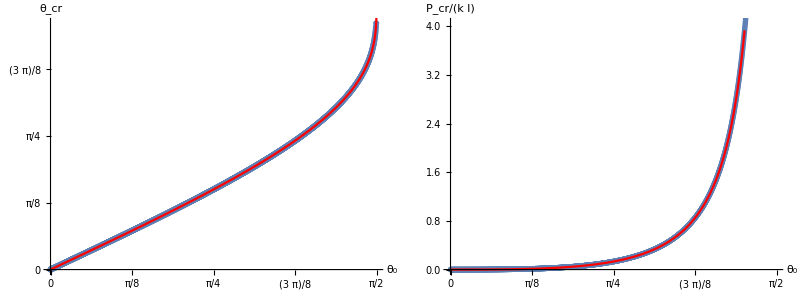

```mathematica
ClearAll[θin, θfin, nel, step, θcr]
θin = 0;
θfin = π/2;
step = 1/1000;
θ1 = Table[θ, {θ,θin, θfin, step}];
nel = (θfin - θin)/step;
θcr = Table[
θ/.FindRoot[
D[λ0[θ, θ1[[i]]] == 0, θ],
 {θ, θ1[[i]]}],
 {i, 1, nel}];

λcr = Table[λ0[θcr[[i]], θ1[[i]]], {i, 1, nel}];

Grid[{{
Show[
ListPlot[
Table[{θ1[[i]], θcr[[i]]}, {i, 1, nel}],
AxesLabel->{"θ_0", "θ_cr"},LabelStyle->18,
Ticks->{Table[k*Pi, {k,0, 1/2, 1/16}], Table[k*Pi, {k,0, 1/2, 1/16}]},
PlotMarkers->Automatic
],
Plot[ArcCos[Cos[θ0]^(1/3)], {θ0, 0, Pi/2}, PlotStyle->Red],
ImageSize->480],

Show[
ListPlot[
Table[{θ1[[i]], λcr[[i]]}, {i, 1, nel}],
AxesLabel->{"θ_0", "P_cr/(k l)"},LabelStyle->18,
Ticks->{Table[k*Pi, {k,0, 1/2, 1/16}], Automatic},
PlotMarkers->●,
ImageSize->480
],
Plot[λ0[ArcCos[Cos[θ0]^(1/3)], θ0], {θ0, 0, Pi/2}, PlotStyle->Red]
]
}}, Spacings->8]
```

## Non-autonomous system

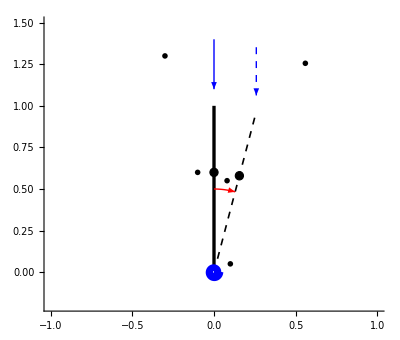

```mathematica
l=1;

carh=Graphics[Triangle[{{-1/2,-1},{0,0},{1/2,-1}}]];
cer=Graphics[{FaceForm[White],EdgeForm[Directive[Thick]],Disk[{0,0},1]}];
myCircle[o_,r_,{a_,b_},res_]:=Arrow@Table[{Cos[k],Sin[k]}*r+o,{k,a,b,(b-a)/res}];
rspring[centre_,rounds_,radius_]:=Module[{},
x[t_]:=radius/rounds/(2*Pi)*t*Cos[t];
y[t_]:=radius/rounds/(2*Pi)*t*Sin[t];
ParametricPlot[{centre[[1]]+x[t],centre[[2]]+y[t]},{t,0,rounds*2*Pi},PlotStyle->Blue]
];

Show[{
Graphics[{Thickness[0.006],Line[{{0,0},{l*Sin[θ],l*Cos[θ]}/.θ->0}]}],
Graphics[{Thickness[0.003],Dashed,Line[{{0,0},{l*Sin[θ],l*Cos[θ]}/.θ->15 Degree}]}],
Graphics[{Inset[cer,{0,0},{0,0},0.05]}],
rspring[{0,0},4,0.05],
Graphics[Text[MaTeX["\\textcolor{blue}{K}",Magnification->2],{0.1,0.05}*l]],
Graphics[{Thick,Blue,Arrow[l*{{0,1.4},{0,1.1}}]}],
Graphics[Text[MaTeX["\\textcolor{blue}{P + Q\,\\cos\\left(\\omega t\\right)}",Magnification->2],{-0.3,1.3}*l]],
Graphics[{Thick,Dashed,Blue,Arrow[{{l*Sin[θ],1.4*l*Cos[θ]}/.θ->15 Degree,{l*Sin[θ],1.1*l*Cos[θ]}/.θ->15 Degree}]}],
Graphics[Text[MaTeX["\\textcolor{blue}{P + Q\,\\cos\\left(\\omega t\\right)}",Magnification->2],{l*Sin[θ]+0.3,1.3*l*Cos[θ]}/.θ->15 Degree]],
Graphics[{FaceForm[Black],EdgeForm[Directive[Thick]],Disk[{0,.6*l},0.025]}],
Graphics[{FaceForm[Black],EdgeForm[Directive[Thick]],Disk[.6*{l*Sin[θ],l*Cos[θ]}/.θ->15 Degree,0.025]}],
Graphics[Text[MaTeX["m",Magnification->2],{-0.1,.6}*l]],
Graphics[{Red,Thick,Arrowheads[0.03],myCircle[{0,0},0.5*l,{90 Degree,75 Degree},10]}],
Graphics[Text[MaTeX["\\textcolor{red}{\\theta}",Magnification->2],{0.08,0.55}*l]]
},
PlotRange->{{-l,l},{-0.2*l,1.5*l}},
Axes->True,
ImageSize->{Automatic,500}]
```

## Linearized system (Mathieu equation)

```mathematica
Clear["Global`*"]
rq = 1/3;(* Subscript[ω, 1]^2/ω^2 *)
p = 1.1;(* P/Subscript[P, cr] *)
q = .1;(* Q/Subscript[P, cr] *)
τfin = 200;
dt = 1/1000;
θ0 = 10^-8;
{a = 1/rq*(1-p), b = -q/rq}
sol = NDSolve[{ θ1[τ] == θ'[τ],θ1'[τ] + (a+b*Cos[τ])*θ[τ]==0, θ[0] == θ0, θ'[0] == 0}, {θ, θ1}, {τ, τfin}, MaxStepSize->dt];

Grid[{{
ParametricPlot[{θ[τ], θ1[τ]}/.sol, {τ, 0, τfin}, AxesLabel->{"θ", OverDot[θ]},LabelStyle->18, PlotRange->Full, ImageSize->Medium],
ParametricPlot[{Extract[Evaluate[θ[τ]/.sol,{1}]], p+q*Cos[τ]}, {τ, 0, τfin}, AxesLabel->{"θ","(P l)/K"},LabelStyle->18,ImageSize->Medium,PlotRange->{{-π,π},{Min[1.5(p-q),0],1.5(p+q)}}],
Plot[Evaluate[{θ[τ]}/.sol],{τ,0,τfin},PlotRange->All,PlotStyle->{Red, Blue},AxesLabel->{"ω t","θ"},LabelStyle->18,ImageSize->Medium]
}},
Spacings->6
]
```

{-0.3,-0.3}

-Graphics- | -Graphics- | -Graphics-

## Non-linearized system

```mathematica
Clear["Global`*"]
rq = 1/3;(* Subscript[ω, 1]^2/ω^2 *)
p = 1.1;(* P/Subscript[P, cr] *)
q = .1;(* Q/Subscript[P, cr] *)
τfin = 200;
dt = 1/1000;
θ0 = 10^-8;
{a = 1/rq*(1-p), b = -q/rq}
sol = NDSolve[{ θ1[τ] == θ'[τ],θ1'[τ] + (a+b*Cos[τ])*Sin[θ[τ]]==0, θ[0] == θ0, θ'[0] == 0}, {θ, θ1}, {τ, τfin}, MaxStepSize->dt];

Grid[{{
Show[
ParametricPlot[{θ[τ], θ1[τ]}/.sol, {τ, 0, τfin}, AxesLabel->{"θ", OverDot[θ]},LabelStyle->18, PlotRange->Full, ImageSize->Medium],
ListPlot[{{θ0,0}},ColorFunction->Red]],
ParametricPlot[{Extract[Evaluate[θ[τ]/.sol,{1}]], p+q*Cos[τ]}, {τ, 0, τfin}, AxesLabel->{"θ","(P l)/K"},LabelStyle->18,ImageSize->Medium,PlotRange->{{-π,π},{Min[1.5(p-q),0],1.5(p+q)}}],
Plot[Evaluate[{θ[τ]}/.sol],{τ,0,τfin},PlotRange->All,PlotStyle->{Red, Blue},AxesLabel->{"ω t","θ"},LabelStyle->18,ImageSize->Medium]
}},
Spacings->6
]
```

{-0.3,-0.3}

-Graphics-

# N DOF systems

## 2 DOF system

## Energetic method

```mathematica
ClearAll["Global`*"]
dof = 2;

V[θ1_, θ2_] = 1/2*θ1^2 + 1/2*(θ2-θ1)^2-λ/2*(2-Cos[θ1]-Cos[θ2]);
dV[λ_,θ1_, θ2_]=Grad[V[θ1, θ2], {θ1, θ2}];
dVlin[λ_,θ1_, θ2_] = Series[Series[dV[λ,θ1, θ2], {θ2, 0, 1}], {θ1, 0, 1}]//Normal
{B, M[λ_]} = CoefficientArrays[{dVlin[λ,θ1,θ2][[1]]==0,dVlin[λ,θ1,θ2][[2]]==0} ,{θ1, θ2}]//Normal;
```

{-θ2+θ1 (2-λ/2),-θ1+θ2 (1-λ/2)}

```mathematica
λcr = λ/.Solve[Det[M[λ]]==0, λ]
```

{3-√5,3+√5}

```mathematica
eq1[λ_] = M[λ] [[1]];
eq2[λ_] = M[λ] [[2]];
θcr1 = θ1/.Solve[eq1[λcr[[1]]].{θ1, θ2}==0, {θ1}][[1]]/.θ2->1
θcr2 = θ2/.Solve[eq2[λcr[[2]]].{θ1, θ2}==0, {θ2}][[1]]/.θ1->1
```

2/(1+√5)

-2/(1+√5)

```mathematica
v1a = {θcr1,1}
v2a = {1, θcr2}

v1 = v1a*θ2;
v2 = v2a*θ1;
```

{2/(1+√5),1}

{1,-2/(1+√5)}

```mathematica
disp1 = {{0,0}, {Sin[v1a[[1]]],Cos[v1a[[1]]]}, {Sin[v1a[[1]]] +Sin[v1a[[2]]] ,Cos[v1a[[1]]]+Cos[v1a[[2]]]}};
disp2 =  {{0,0}, {Sin[v2a[[1]]],Cos[v2a[[1]]]}, {Sin[v2a[[1]]] +Sin[v2a[[2]]] ,Cos[v2a[[1]]]+Cos[v2a[[2]]]}};
```

```mathematica
Show[
ListLinePlot[{disp1}, PlotRange->{{-1,1.2}, {0, 2}},PlotMarkers->{"◆", 18}, PlotLabels->"Mode I", PlotStyle->Blue, LabelStyle->18],
ListLinePlot[{disp2}, PlotRange->{{-1,1.}, {0,2}},PlotMarkers->{"■", 18}, PlotLabels->"Mode II", PlotStyle->Red, LabelStyle->18], 
Graphics[
Arrow[{
disp1[[3]]+{0,.5},
disp1[[3]]
}]
],
Graphics[
Arrow[{
disp2[[3]]+{0,.5},
disp2[[3]]
}]
],
Graphics[
Text[Style["P",Large ],disp1[[3]]+{0.1,.25}]
],
Graphics[
Text[Style["P",Large ],disp2[[3]]+{0.1,.25}]
],
ImageSize->Large, AspectRatio->1
]
```

-Graphics-

```mathematica
λ1 = λ/.Solve[dV[λ,θ1, θ2][[1]]==0, λ][[1]]
```

2 (2 θ1-θ2) Csc[θ1]

```mathematica
dV[λ,θ1, θ2][[2]]/.λ->λ1//FullSimplify
dV[λ,θ1, θ2][[2]]//FullSimplify
```

-θ1+θ2+(-2 θ1+θ2) Csc[θ1] Sin[θ2]

-θ1+θ2-1/2 λ Sin[θ2]

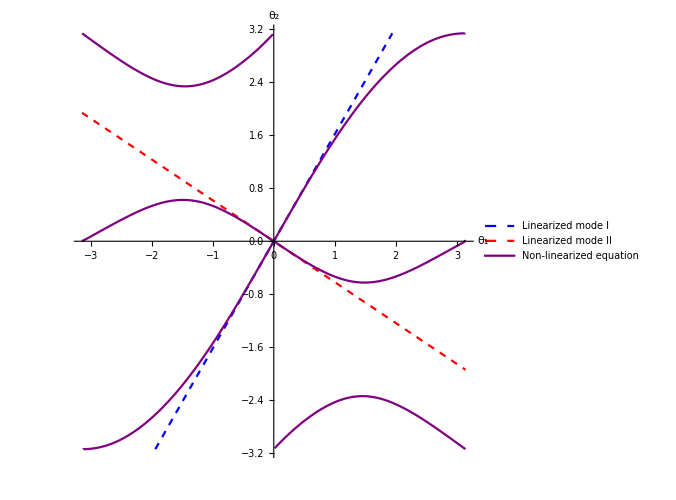
-Graphics3D- | -Graphics-

```mathematica
u1 = {v1[[1]], v1[[2]], λcr[[1]]};
u2 = {v2[[1]], v2[[2]], λcr[[2]]};
Grid[{{
Show[
ParametricPlot3D[{u1,u2},{θ1, -Pi, Pi} ,{θ2, -Pi, Pi}, PlotRange->{{-Pi, Pi},{-Pi, Pi}, Automatic}, AxesLabel->{"θ_1", "θ_2", "(P l)/K"}, LabelStyle->18,PlotStyle->{EdgeForm[{Blue,Thick}],EdgeForm[{Red,Thick}]}, PlotPoints->{20,20}, PlotLabels->{"Mode I", "Mode II"}, ImageSize->500, AspectRatio->1]
(*,
ContourPlot3D[-θ1+θ2-1/2 λ Sin[θ2]==0, {θ1, -Pi, Pi},{θ2, -Pi, Pi}, {λ, 0, 2},ContourStyle->Purple,AspectRatio->1,PlotPoints->20]
*)
],
Show[
ParametricPlot[v1, {θ2, -Pi, Pi}, PlotRange->{{-Pi, Pi}, Automatic}, AxesLabel->{"θ_1", "θ_2"},LabelStyle->18, PlotStyle->{Dashed,Blue} ,PlotLegends->{"Linearized mode I"}],
ParametricPlot[v2, {θ1, -Pi, Pi}, PlotRange->{{-Pi, Pi}, Automatic},PlotStyle->{Dashed,Red},PlotLegends->{"Linearized mode II"}],
ContourPlot[-θ1+θ2+(-2 θ1+θ2) Csc[θ1] Sin[θ2]==0, {θ1, -Pi, Pi},{θ2, -Pi, Pi},Axes->True,ContourStyle->Purple,AspectRatio->1,PlotPoints->50,PlotLegends->{"Non-linearized equation"}],
ImageSize->500
]
}}, Spacings->5]
```

```mathematica
H= Grad[dV[λ, θ1, θ2], {θ1, θ2}];
MatrixForm[H]

Hlin = Grad[dVlin[λ, θ1, θ2], {θ1, θ2}];
MatrixForm[Hlin]
```

(2-1/2 λ Cos[θ1] | -1
-1 | 1-1/2 λ Cos[θ2])

(2-λ/2 | -1
-1 | 1-λ/2)

```mathematica
Det[Hlin/.λ->λcr[[1]]]
Det[Hlin/.λ->λcr[[2]]]
```

0

0

```mathematica
dV[λ, 0, 0]
```

{0,0}

```mathematica
eigv1 = {Eigenvalues[H/.θ1->0/.θ2->0/.λ->λcr[[1]]],
Eigenvalues[H/.θ1->0/.θ2->0/.λ->λcr[[2]]]}
```

{{√5,0},{-√5,0}}

```mathematica
Table[Table[If[eigv1[[i,j]]<0,Print["Fundamental path is instable"]], {j, 1,2}], {i,1,2}];
```

Fundamental path is instable

```mathematica
Eigenvalues[H/.λ->λcr[[1]]]
Eigenvalues[H/.λ->λcr[[2]]]
```

{1/4 (6-3 Cos[θ1]+√5 Cos[θ1]-3 Cos[θ2]+√5 Cos[θ2]-√((-6+3 Cos[θ1]-√5 Cos[θ1]+3 Cos[θ2]-√5 Cos[θ2])^2-4 (4-6 Cos[θ1]+2 √5 Cos[θ1]+7 Cos[θ1-θ2]-3 √5 Cos[θ1-θ2]-12 Cos[θ2]+4 √5 Cos[θ2]+7 Cos[θ1+θ2]-3 √5 Cos[θ1+θ2]))),1/4 (6-3 Cos[θ1]+√5 Cos[θ1]-3 Cos[θ2]+√5 Cos[θ2]+√((-6+3 Cos[θ1]-√5 Cos[θ1]+3 Cos[θ2]-√5 Cos[θ2])^2-4 (4-6 Cos[θ1]+2 √5 Cos[θ1]+7 Cos[θ1-θ2]-3 √5 Cos[θ1-θ2]-12 Cos[θ2]+4 √5 Cos[θ2]+7 Cos[θ1+θ2]-3 √5 Cos[θ1+θ2])))}

{1/4 (6-3 Cos[θ1]-√5 Cos[θ1]-3 Cos[θ2]-√5 Cos[θ2]-√((-6+3 Cos[θ1]+√5 Cos[θ1]+3 Cos[θ2]+√5 Cos[θ2])^2-4 (4-6 Cos[θ1]-2 √5 Cos[θ1]+7 Cos[θ1-θ2]+3 √5 Cos[θ1-θ2]-12 Cos[θ2]-4 √5 Cos[θ2]+7 Cos[θ1+θ2]+3 √5 Cos[θ1+θ2]))),1/4 (6-3 Cos[θ1]-√5 Cos[θ1]-3 Cos[θ2]-√5 Cos[θ2]+√((-6+3 Cos[θ1]+√5 Cos[θ1]+3 Cos[θ2]+√5 Cos[θ2])^2-4 (4-6 Cos[θ1]-2 √5 Cos[θ1]+7 Cos[θ1-θ2]+3 √5 Cos[θ1-θ2]-12 Cos[θ2]-4 √5 Cos[θ2]+7 Cos[θ1+θ2]+3 √5 Cos[θ1+θ2])))}

```mathematica
Plot3D[{
1/4 (6-3 Cos[θ1]+√5 Cos[θ1]-3 Cos[θ2]+√5 Cos[θ2]-√((-6+3 Cos[θ1]-√5 Cos[θ1]+3 Cos[θ2]-√5 Cos[θ2])^2-4 (4-6 Cos[θ1]+2 √5 Cos[θ1]+7 Cos[θ1-θ2]-3 √5 Cos[θ1-θ2]-12 Cos[θ2]+4 √5 Cos[θ2]+7 Cos[θ1+θ2]-3 √5 Cos[θ1+θ2]))),1/4 (6-3 Cos[θ1]+√5 Cos[θ1]-3 Cos[θ2]+√5 Cos[θ2]+√((-6+3 Cos[θ1]-√5 Cos[θ1]+3 Cos[θ2]-√5 Cos[θ2])^2-4 (4-6 Cos[θ1]+2 √5 Cos[θ1]+7 Cos[θ1-θ2]-3 √5 Cos[θ1-θ2]-12 Cos[θ2]+4 √5 Cos[θ2]+7 Cos[θ1+θ2]-3 √5 Cos[θ1+θ2]))),
1/4 (6-3 Cos[θ1]-√5 Cos[θ1]-3 Cos[θ2]-√5 Cos[θ2]-√((-6+3 Cos[θ1]+√5 Cos[θ1]+3 Cos[θ2]+√5 Cos[θ2])^2-4 (4-6 Cos[θ1]-2 √5 Cos[θ1]+7 Cos[θ1-θ2]+3 √5 Cos[θ1-θ2]-12 Cos[θ2]-4 √5 Cos[θ2]+7 Cos[θ1+θ2]+3 √5 Cos[θ1+θ2]))),1/4 (6-3 Cos[θ1]-√5 Cos[θ1]-3 Cos[θ2]-√5 Cos[θ2]+√((-6+3 Cos[θ1]+√5 Cos[θ1]+3 Cos[θ2]+√5 Cos[θ2])^2-4 (4-6 Cos[θ1]-2 √5 Cos[θ1]+7 Cos[θ1-θ2]+3 √5 Cos[θ1-θ2]-12 Cos[θ2]-4 √5 Cos[θ2]+7 Cos[θ1+θ2]+3 √5 Cos[θ1+θ2])))
 }, {θ1, -Pi, Pi}, {θ2, -Pi, Pi}, AxesLabel->{"θ_1", "θ_2", "Eigenvalues λ_i"}, LabelStyle->18, ImageSize->Large]
```

-Graphics3D-

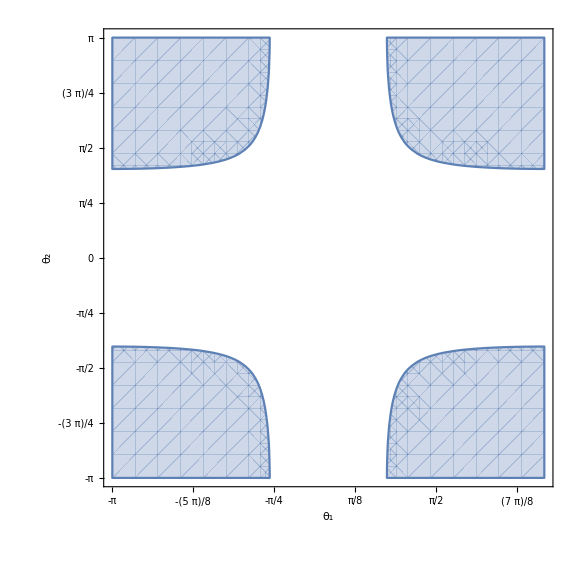

```mathematica
RegionPlot[{
1/4 (6-3 Cos[θ1]+√5 Cos[θ1]-3 Cos[θ2]+√5 Cos[θ2]-√((-6+3 Cos[θ1]-√5 Cos[θ1]+3 Cos[θ2]-√5 Cos[θ2])^2-4 (4-6 Cos[θ1]+2 √5 Cos[θ1]+7 Cos[θ1-θ2]-3 √5 Cos[θ1-θ2]-12 Cos[θ2]+4 √5 Cos[θ2]+7 Cos[θ1+θ2]-3 √5 Cos[θ1+θ2])))>0&&1/4 (6-3 Cos[θ1]+√5 Cos[θ1]-3 Cos[θ2]+√5 Cos[θ2]+√((-6+3 Cos[θ1]-√5 Cos[θ1]+3 Cos[θ2]-√5 Cos[θ2])^2-4 (4-6 Cos[θ1]+2 √5 Cos[θ1]+7 Cos[θ1-θ2]-3 √5 Cos[θ1-θ2]-12 Cos[θ2]+4 √5 Cos[θ2]+7 Cos[θ1+θ2]-3 √5 Cos[θ1+θ2])))>0&&
1/4 (6-3 Cos[θ1]-√5 Cos[θ1]-3 Cos[θ2]-√5 Cos[θ2]-√((-6+3 Cos[θ1]+√5 Cos[θ1]+3 Cos[θ2]+√5 Cos[θ2])^2-4 (4-6 Cos[θ1]-2 √5 Cos[θ1]+7 Cos[θ1-θ2]+3 √5 Cos[θ1-θ2]-12 Cos[θ2]-4 √5 Cos[θ2]+7 Cos[θ1+θ2]+3 √5 Cos[θ1+θ2])))>0&&1/4 (6-3 Cos[θ1]-√5 Cos[θ1]-3 Cos[θ2]-√5 Cos[θ2]+√((-6+3 Cos[θ1]+√5 Cos[θ1]+3 Cos[θ2]+√5 Cos[θ2])^2-4 (4-6 Cos[θ1]-2 √5 Cos[θ1]+7 Cos[θ1-θ2]+3 √5 Cos[θ1-θ2]-12 Cos[θ2]-4 √5 Cos[θ2]+7 Cos[θ1+θ2]+3 √5 Cos[θ1+θ2])))>0
 }, {θ1, -Pi, Pi}, {θ2, -Pi, Pi}, FrameLabel->{"θ_1", "θ_2"},FrameTicks->{Table[k*Pi, {k, -1, 1, 1/8}],Table[k*Pi, {k, -1, 1, 1/8}]}, LabelStyle->18, ImageSize->Large, Axes->True]
```

## Dynamic method (P_x = 0, P_y = P)

```mathematica
M = {
{2-p-2*m*Ω, -1-m*Ω},
{-1-m*Ω, 1-p-m*Ω}
};
MatrixForm[M]
```

(2-p-2 m Ω | -1-m Ω
-1-m Ω | 1-p-m Ω)

```mathematica
Ωcr = Ω/.Solve[Det[M]==0, Ω]//FullSimplify
```

{-(-6+3 p+√(32+p (-24+5 p)))/(2 m),(6-3 p+√(32+p (-24+5 p)))/(2 m)}

```mathematica
pcr = 2*ArrayReshape[p/.Table[Solve[Ωcr[[i]]==0, p], {i, 2}], {1,2}][[1]]
```

{3-√5,3+√5}

```mathematica
p0 =2*(p/.Solve[Ω-Ωcr[[1]]==0, p])
```

{3-3 m Ω-√(5+6 m Ω+5 m^2 Ω^2),3-3 m Ω+√(5+6 m Ω+5 m^2 Ω^2)}

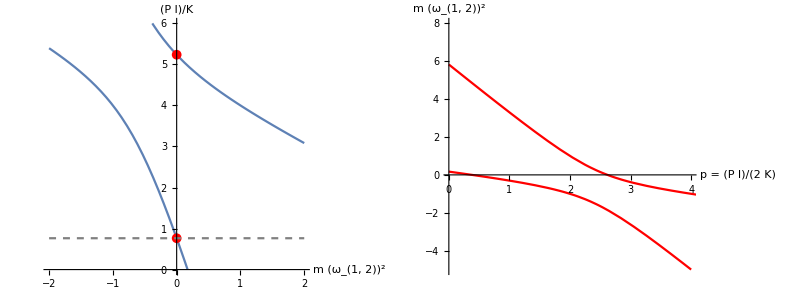

```mathematica
Grid[{{
Show[
Plot[p0/.m->1,{Ω,-2,2}, AxesLabel->{"m (ω_(1, 2))^2","(P l)/K"},LabelStyle->18,PlotRange->{Automatic, {0,6}}, ImageSize->500, AspectRatio->Full ],
ListPlot[{{0,pcr[[1]]}, {0, pcr[[2]]}}, PlotStyle->{Red}, PlotMarkers->{Automatic, Medium}],
Plot[pcr[[1]],{Ω,-2,2}, PlotStyle->{Gray, Dashed}]

],
Plot[Ωcr/.m->1, {p, 0, 10}, AxesLabel->{"p = (P l)/(2  K)", "m (ω_(1, 2))^2"},LabelStyle->18,PlotRange->{{0, 4}, {-5,8}}, ImageSize->500, AspectRatio->Full, PlotStyle->{Blue, Red}]
}}]
```

## Dynamic method (P_x(θ_1, θ_2) = P_x(θ_2), P_y(θ_1, θ_2) = P_y(θ_2))

```mathematica
ClearAll["Global`*"]
```

```mathematica
M = {
{2-p-2*m*Ω, -1+p-m*Ω},
{-1-m*Ω, 1-m*Ω}
};
MatrixForm[M]
```

(2-p-2 m Ω | -1+p-m Ω
-1-m Ω | 1-m Ω)

```mathematica
Ωcr = Ω/.Solve[Det[M]==0, Ω]//Simplify
```

{-(m (-3+p)+√(m^2 (8-6 p+p^2)))/m^2,(3 m-m p+√(m^2 (8-6 p+p^2)))/m^2}

```mathematica
pcr =2*ArrayReshape[Table[(p/.Solve[{Ω-Ωcr[[i]]==0}, p]), {i,2}], {1,2}][[1]]
```

{(-1+6 m Ω-m^2 Ω^2)/(m Ω),(-1+6 m Ω-m^2 Ω^2)/(m Ω)}

```mathematica
Ω/.Solve[D[pcr, Ω] == 0, Ω]/.m->1
pcr[[1]]/.Ω->1/.m->1
pcr[[1]]/.Ω->-1/.m->1
```

{-1,1}

4

8

```mathematica
Ωcr/.p->3.99/.m->1//N (* Flutter zone -> Complex number *)
```

{-0.99-0.141067 ⅈ,-0.99+0.141067 ⅈ}

```mathematica
b = (Im[Table[{k,Ωcr[[2]]}/.p->k/.m->1, {k, 2, 4, .1}]] + Table[{k,0}, {k, 2,4,.1}]) (* Imaginary part *)
bt = (Im[Table[{Ωcr[[2]],k}/.p->k/.m->1, {k, 2, 4, .1}]] + Table[{0,2*k}, {k, 2,4,.1}]) (* Imaginary part *)
```

{{2.,0},{2.1,0.43589},{2.2,0.6},{2.3,0.714143},{2.4,0.8},{2.5,0.866025},{2.6,0.916515},{2.7,0.953939},{2.8,0.979796},{2.9,0.994987},{3.,1.},{3.1,0.994987},{3.2,0.979796},{3.3,0.953939},{3.4,0.916515},{3.5,0.866025},{3.6,0.8},{3.7,0.714143},{3.8,0.6},{3.9,0.43589},{4.,0}}

{{0,4.},{0.43589,4.2},{0.6,4.4},{0.714143,4.6},{0.8,4.8},{0.866025,5.},{0.916515,5.2},{0.953939,5.4},{0.979796,5.6},{0.994987,5.8},{1.,6.},{0.994987,6.2},{0.979796,6.4},{0.953939,6.6},{0.916515,6.8},{0.866025,7.},{0.8,7.2},{0.714143,7.4},{0.6,7.6},{0.43589,7.8},{0,8.}}

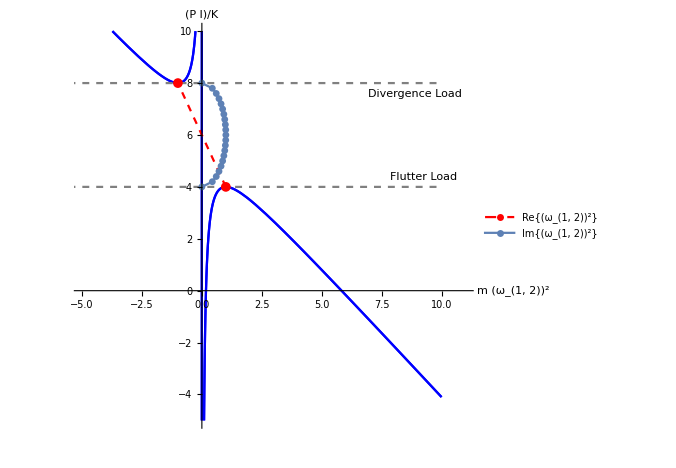
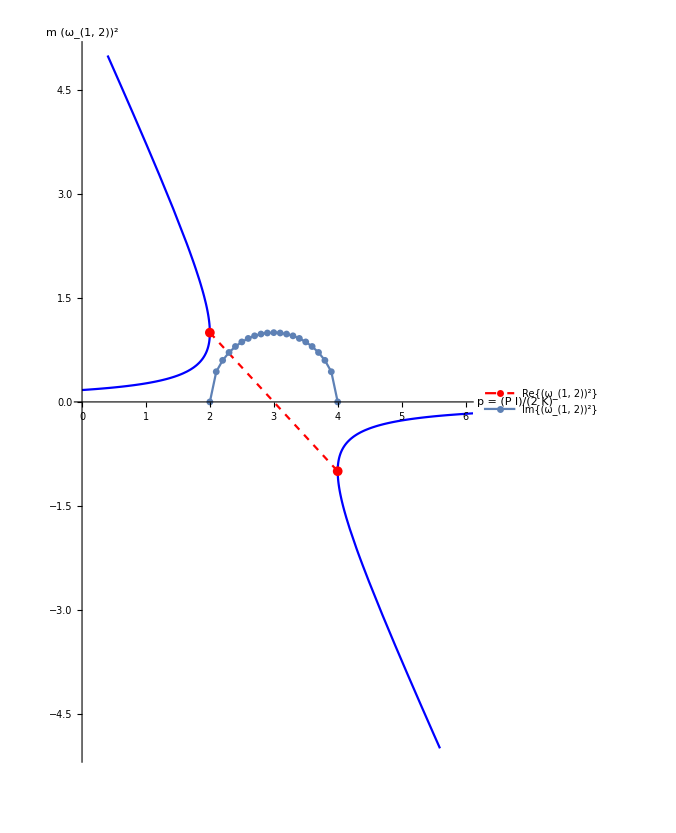
-Graphics- | -Graphics-

```mathematica
Grid[{{
Show[
Plot[pcr/.m->1,{Ω,-10,10}, AxesLabel->{"m (ω_(1, 2))^2","(P l)/K"},LabelStyle->18,PlotRange->{{-5,11}, {-5,10}}, ImageSize->500, AspectRatio->Full, PlotStyle->Blue ],
Plot[{Evaluate[pcr[[1]]/.Ω->1/.m->1 ], Evaluate[pcr[[1]]/.Ω->-1/.m->1 ]}, {Ω, -10, 10}, PlotStyle->{{Gray, Dashed}, {Gray, Dashed}}, PlotLabels->Placed[{"Flutter Load", "Divergence Load"},Right]],
ListLinePlot[{{Ω,pcr[[1]]/.m->1}/.Ω->1, {Ω,pcr[[1]]/.m->1}/.Ω->-1}, PlotStyle->{Red, Dashed}, PlotMarkers->{Automatic, Medium},  PlotLegends->{"Re{(ω_(1, 2))^2}"}],
ListLinePlot[bt, PlotStyle->{Automatic}, PlotMarkers->{Automatic, Small},  PlotLegends->{"Im{(ω_(1, 2))^2}"}]
],
Show[
Plot[Ωcr/.m->1, {p, 0, 10}, AxesLabel->{"p = (P l)/(2  K)", "m (ω_(1, 2))^2"},LabelStyle->18,PlotRange->{{0,6}, {-5,5}}, ImageSize->500, AspectRatio->Full, PlotStyle->{Blue}],
ListLinePlot[{{pcr[[1]]/2, Ω}/.m->1/.Ω->1, {pcr[[1]]/2, Ω}/.m->1/.Ω->-1}, PlotStyle->{Red, Dashed}, PlotMarkers->{Automatic, Medium},  PlotLegends->{"Re{(ω_(1, 2))^2}"}],
ListLinePlot[b, PlotStyle->{Automatic}, PlotMarkers->{Automatic, Small},  PlotLegends->{"Im{(ω_(1, 2))^2}"}]
]
}}]
```

## Augusti model

```mathematica
ClearAll["Global`*"]
```

```mathematica
V[λ_, θ1_, θ2_]=1/2*θ1^2+1/2*rk*θ2^2 - λ(1-Sqrt[1-Sin[θ1]^2-Sin[θ2]^2]);
dV[λ_, θ1_, θ2_] = D[V[λ, θ1, θ2], {{θ1,θ2},1}]//Simplify
```

{θ1-(√2 λ Cos[θ1] Sin[θ1])/(√(Cos[2 θ1]+Cos[2 θ2])),rk θ2-(√2 λ Cos[θ2] Sin[θ2])/(√(Cos[2 θ1]+Cos[2 θ2]))}

```mathematica
{λ1, λ2} = {λ/.Solve[dV[λ, θ1, 0][[1]]==0, λ][[1]], λ/.Solve[dV[λ, 0, θ2][[2]]==0, λ][[1]]}
```

{(θ1 √(1+Cos[2 θ1]) Csc[θ1] Sec[θ1])/(√2),(rk θ2 √(1+Cos[2 θ2]) Csc[θ2] Sec[θ2])/(√2)}

```mathematica
Manipulate[
Plot3D[{λ1, λ2}, {θ1, -Pi/2, Pi/2}, {θ2, -Pi/2, Pi/2}], 
{rk, 0, 2}]
```